```mathematica
Quit[]
```

```mathematica
Uninstall[link]
```

'/phenod/x3/bednya/mr/mr/math/mr'

```mathematica
Quit[]
```

```mathematica
<<"mr_lib.m"
```

MR - Matching and Running Mathmatica interface

To see available functions use Names["mr`*"]

Andrey Pikelner <pikelner@theor.jinr.ru>

#### Old

```mathematica
s91=sol[PDG`MZ][]
```

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
s172=sol[PDG`MT][]
```

{gp→0.359473,g→0.649242,gs→1.16499,yt→0.961668,lam→0.128094,mu0→132.47,mu→173.21}

```mathematica
s91explmv = RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. s91,PDG`MZ]
```

{gp→0.3497 corr(h^2 (-0.00263351 as aw-0.00152161 aw^2)+0.0249616 aw h+1.,0.357008),g→0.652954 corr(h^2 (0.0000806233 as aw+0.000523887 aw^2)-0.00286806 aw h+1.,0.651477),gs→1.21442 corr(1.,1.21442),yb→0.165695 corr(h^2 (-0.0468244 as^2+0.000904795 as aw+0.000150551 aw^2)+h (-0.135054 as-0.00507558 aw)+1.,0.130054),yt→0.99743 corr(h^2 (-0.00288167 as^2-0.000487094 as aw+0.000619437 aw^2)+h (-0.000936964 as-0.00631505 aw)+1.,0.98599),lam→0.130315 corr(h^2 (-0.0218564 as aw-0.0208252 aw^2)+0.124333 aw h+1.,0.140956),ms→125.7 corr(h^2 (-0.00437885 as aw-0.00732411 aw^2)+0.0490884 aw h+1.,130.461),vev→246.22 corr(h^2 (0.00654936 as aw+0.00583444 aw^2)-0.0130843 aw h+1.,246.068),mu→91.1876 corr(1.,91.1876)}

{gp→0.00812283 √(8315.18 (-0.0010487 as aw h^2+0.00028118 aw^2 h^2+0.00667021 aw h+1)-6461.75 (0.000161247 as aw h^2+0.001056 aw^2 h^2-0.00573612 aw h+1)),g→0.652954 √(0.000161247 as aw h^2+0.001056 aw^2 h^2-0.00573612 aw h+1),gs→1.21442,yb→0.165695 √(-0.0317748 as^3 h^3-0.0754093 as^2 h^2+0.00318054 as aw h^2-0.270107 as h+0.000326863 aw^2 h^2-0.0101512 aw h+1),yt→0.99743 √(-0.00285811 as^3 h^3-0.00576247 as^2 h^2-0.000962354 as aw h^2-0.00187393 as h+0.00127875 aw^2 h^2-0.0126301 aw h+1),lam→0.130315 (-0.0218564 as aw h^2-0.0208252 aw^2 h^2+0.124333 aw h+1),ms→125.7 √(-0.00875771 as aw h^2-0.0122385 aw^2 h^2+0.0981768 aw h+1),vev→246.22 √(0.0130987 as aw h^2+0.0118401 aw^2 h^2-0.0261685 aw h+1),mu→91.1876}

{gp→0.00812283 √(8315.18 (-0.0010487 as aw h^2+0.00028118 aw^2 h^2+0.00667021 aw h+1)-6461.75 (0.000161247 as aw h^2+0.001056 aw^2 h^2-0.00573612 aw h+1)),g→0.652954 √(0.000161247 as aw h^2 lkkjлоk+0.001056 aw^2 h^2-0.00573612 aw h+1),gs→1.21442,yb→0.165695 √(-0.0317748 as^3 h^3-0.0754093 as^2 h^2+0.00318054 as aw h^2-0.270107 as h+0.000326863 aw^2 h^2-0.0101512 aw h+1),yt→0.99743 √(-0.00285811 as^3 h^3-0.00576247 as^2 h^2-0.000962354 as aw h^2-0.00187393 as h+0.00127875 aw^2 h^2-0.0126301 aw h+1),lam→0.130315 (-0.0218564 as aw h^2-0.0208252 aw^2 h^2+0.124333 aw h+1),ms→125.7 √(-0.00875771 as aw h^2-0.0122385 aw^2 h^2+0.0981768 aw h+1),vev→246.22 √(0.0130987 as aw h^2+0.0118401 aw^2 h^2-0.0261685 aw h+1),mu→91.1876}

{gp→0.3497 corr(h^2 (-0.00263351 as aw-0.00152161 aw^2)+h^3 (0.0000657368 as aw^2+0.0000379818 aw^3+0.)+0.0249616 aw h+1.,0.357008),g→0.652954 corr(h^2 (0.0000806233 as aw+0.000523887 aw^2)+h^3 (2.31232×10^-7 as aw^2+1.50254×10^-6 aw^3+0.)-0.00286806 aw h+1.,0.651477),gs→1.21442 corr(1.,1.21442),yb→0.165695 corr(h^2 (-0.0468244 as^2+0.000904795 as aw+0.000150551 aw^2)+h^3 (-0.0222112 as^3-0.000115465 as^2 aw+0.0000249248 as aw^2+7.64134×10^-7 aw^3)+h (-0.135054 as-0.00507558 aw)+1.,0.130054),yt→0.99743 corr(h^2 (-0.00288167 as^2-0.000487094 as aw+0.000619437 aw^2)+h^3 (-0.00143175 as^3-0.0000186543 as^2 aw-2.49563×10^-6 as aw^2+3.91177×10^-6 aw^3)+h (-0.000936964 as-0.00631505 aw)+1.,0.98599),lam→0.130315 corr(h^2 (-0.0218564 as aw-0.0208252 aw^2)+0.124333 aw h+1.,0.140956),ms→125.7 corr(h^2 (-0.00437885 as aw-0.00732411 aw^2)+h^3 (0.000214951 as aw^2+0.000359529 aw^3+0.)+0.0490884 aw h+1.,130.461),vev→246.22 corr(h^2 (0.00654936 as aw+0.00583444 aw^2)+h^3 (0.0000856936 as aw^2+0.0000763393 aw^3+0.)-0.0130843 aw h+1.,246.068),mu→91.1876 corr(1.,91.1876)}

{gp→0.3497 corr(h^2 (-0.00263351 as aw-0.00152161 aw^2)+0.0249616 aw h+1.,0.357008),g→0.652954 corr(h^2 (0.0000806233 as aw+0.000523887 aw^2)-0.00286806 aw h+1.,0.651477),gs→1.21442 corr(1.,1.21442),yb→0.165695 corr(h^2 (-0.0468244 as^2+0.000904795 as aw+0.000150551 aw^2)+h (-0.135054 as-0.00507558 aw)+1.,0.130054),yt→0.99743 corr(h^2 (-0.00288167 as^2-0.000487094 as aw+0.000619437 aw^2)+h (-0.000936964 as-0.00631505 aw)+1.,0.98599),lam→0.130315 corr(h^2 (-0.0218564 as aw-0.0208252 aw^2)+0.124333 aw h+1.,0.140956),ms→125.7 corr(h^2 (-0.00437885 as aw-0.00732411 aw^2)+0.0490884 aw h+1.,130.461),vev→246.22 corr(h^2 (0.00654936 as aw+0.00583444 aw^2)-0.0130843 aw h+1.,246.068),mu→91.1876 corr(1.,91.1876)}

```mathematica
yt
```

yt

```mathematica
s91ex = s91explmv /. z_ corr[x__,y_]:> y
```

{gp→0.357008,g→0.651477,gs→1.21442,yb→0.130054,yt→0.98599,lam→0.140956,ms→130.461,vev→246.068,mu→91.1876}

```mathematica
{Sqrt[2 lam vev^2 /. s91ex],ms /. s91ex, mu0 /. s91}
```

{130.651,130.461,130.852}

```mathematica
Sqrt[2 lam vev^2 /. s91ex]
```

130.651

```mathematica
s172explmv = RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. s172,PDG`MT]
```

{gp→0.3497 corr(h^2 (-0.00236713 as aw-0.00146392 aw^2)+0.0285632 aw h+1.,0.358383),g→0.652954 corr(h^2 (0.000259365 as aw+0.00087795 aw^2)-0.00855567 aw h+1.,0.648116),gs→1.16499 corr(1.,1.16499),yb→0.165695 corr(h^2 (-0.0507736 as^2+0.000802635 as aw+0.000124263 aw^2)+h (-0.146339 as-0.00408871 aw)+1.,0.1271),yt→0.99743 corr(h^2 (-0.00565514 as^2-0.00019768 as aw+0.000135448 aw^2)+h (0.000648939 aw-0.0229188 as)+1.,0.96769),lam→0.130315 corr(h^2 (-0.0103489 as aw-0.00262025 aw^2)-0.0114081 aw h+1.,0.127138),ms→125.7 corr(h^2 (-0.00392216 as aw-0.00749411 aw^2)+0.0606248 aw h+1.,131.961),vev→246.22 corr(h^2 (0.0012523 as aw-0.00578647 aw^2)+0.0663321 aw h+1.,261.503),mu→173.21 corr(1.,173.21)}

```mathematica
s172ex = s172explmv /. z_ corr[x__,y_]:> y
```

{gp→0.363337,g→0.636523,gs→1.02779,yb→0.118833,yt→0.916774,lam→0.0819254,ms→136.541,vev→340.44,mu→1732.1}

```mathematica
{Sqrt[2 lam vev^2 /. s172ex],ms /. s172ex, mu0 /. s172}
```

{137.805,136.541,136.12}

```mathematica
s172
```

{gp→0.359473,g→0.649242,gs→1.16499,yt→0.961668,lam→0.128094,mu0→132.47,mu→173.21}

```mathematica
s11=sol[100][]
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

```mathematica
test[scale_]:= Module[{ss= sol[scale][]},RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. ss,scale]]
```

```mathematica
TableForm[test[#] & /@ {100,130,160,190,210}]
```

{gp→0.00812283 √(8315.18 (-0.00283131 h^2+0.0117162 h+1)-6461.75 (0.00201106 h^2-0.0155796 h+1)),g→0.652954 √(0.00201106 h^2-0.0155796 h+1),gs→1.20692,yb→0.165695 √(0.00658846 h^2-0.0161523 h+1),yt→0.99743 √(0.00256054 h^2-0.0169405 h+1),lam→0.130315 (-0.0979513 h^2+0.228669 h+1),mu→100}->{gp→0.364622,g→0.648509,gs→1.20692,yb→0.164901,yt→0.990233,lam→0.14735,mu→100}

{gp→0.00812283 √(8315.18 (-0.00212488 h^2+0.00868233 h+1)-6461.75 (0.00274064 h^2-0.0203813 h+1)),g→0.652954 √(0.00274064 h^2-0.0203813 h+1),gs→1.18632,yb→0.165695 √(0.00446443 h^2-0.0100768 h+1),yt→0.99743 √(0.00154436 h^2-0.00583421 h+1),lam→0.130315 (-0.0635115 h^2+0.112998 h+1),mu→130}->{gp→0.365252,g→0.647169,gs→1.18632,yb→0.16523,yt→0.995289,lam→0.136764,mu→130}

{gp→0.00812283 √(8315.18 (-0.00153938 h^2+0.00627423 h+1)-6461.75 (0.00335482 h^2-0.0241922 h+1)),g→0.652954 √(0.00335482 h^2-0.0241922 h+1),gs→1.17077,yb→0.165695 √(0.00262894 h^2-0.00525457 h+1),yt→0.99743 √(0.000365003 h^2+0.00298102 h+1),lam→0.130315 (-0.0371799 h^2+0.0211874 h+1),mu→160}->{gp→0.365748,g→0.646115,gs→1.17077,yb→0.165478,yt→0.999098,lam→0.128231,mu→160}

{gp→0.00812283 √(8315.18 (-0.00103648 h^2+0.00427652 h+1)-6461.75 (0.00388828 h^2-0.0273533 h+1)),g→0.652954 √(0.00388828 h^2-0.0273533 h+1),gs→1.15836,yb→0.165695 √(0.00102204 h^2-0.00125419 h+1),yt→0.99743 √(-0.000827642 h^2+0.0102937 h+1),lam→0.130315 (-0.0163912 h^2-0.0549748 h+1),mu→190}->{gp→0.366158,g→0.645247,gs→1.15836,yb→0.165676,yt→1.00214,lam→0.121015,mu→190}

{gp→0.00812283 √(8315.18 (-0.00073577 h^2+0.00311115 h+1)-6461.75 (0.00420961 h^2-0.0291972 h+1)),g→0.652954 √(0.00420961 h^2-0.0291972 h+1),gs→1.15131,yb→0.165695 √(0.0000539779 h^2+0.00107943 h+1),yt→0.99743 √(-0.00160289 h^2+0.0145595 h+1),lam→0.130315 (-0.00481375 h^2-0.0994036 h+1),mu→210}->{gp→0.366397,g→0.644744,gs→1.15131,yb→0.165789,yt→1.00387,lam→0.116734,mu→210}

gp→0.3497 corr(-0.0112847 h^2+0.0534396 h+1.,0.364622) | g→0.652954 corr(0.000975192 h^2-0.00778978 h+1.,0.648509) | gs→1.20692 corr(1.,1.20692) | yb→0.165695 corr(0.00326162 h^2-0.00807613 h+1.,0.164901) | yt→0.99743 corr(0.0012444 h^2-0.00847024 h+1.,0.990233) | lam→0.130315 corr(-0.0979513 h^2+0.228669 h+1.,0.14735) | mu→100 corr(1,100)
gp→0.3497 corr(-0.0110567 h^2+0.0550045 h+1.,0.365252) | g→0.652954 corr(0.00131839 h^2-0.0101907 h+1.,0.647169) | gs→1.18632 corr(1.,1.18632) | yb→0.165695 corr(0.00221952 h^2-0.00503842 h+1.,0.16523) | yt→0.99743 corr(0.000767924 h^2-0.0029171 h+1.,0.995289) | lam→0.130315 corr(-0.0635115 h^2+0.112998 h+1.,0.136764) | mu→130 corr(1,130)
gp→0.3497 corr(-0.010883 h^2+0.0562458 h+1.,0.365748) | g→0.652954 corr(0.00160425 h^2-0.0120961 h+1.,0.646115) | gs→1.17077 corr(1.,1.17077) | yb→0.165695 corr(0.00131102 h^2-0.00262729 h+1.,0.165478) | yt→0.99743 corr(0.000181391 h^2+0.00149051 h+1.,0.999098) | lam→0.130315 corr(-0.0371799 h^2+0.0211874 h+1.,0.128231) | mu→160 corr(1,160)
gp→0.3497 corr(-0.0107432 h^2+0.057275 h+1.,0.366158) | g→0.652954 corr(0.00185061 h^2-0.0136767 h+1.,0.645247) | gs→1.15836 corr(1.,1.15836) | yb→0.165695 corr(0.000510823 h^2-0.000627095 h+1.,0.165676) | yt→0.99743 corr(-0.000427066 h^2+0.00514685 h+1.,1.00214) | lam→0.130315 corr(-0.0163912 h^2-0.0549748 h+1.,0.121015) | mu→190 corr(1,190)
gp→0.3497 corr(-0.0106634 h^2+0.0578751 h+1.,0.366397) | g→0.652954 corr(0.00199825 h^2-0.0145986 h+1.,0.644744) | gs→1.15131 corr(1.,1.15131) | yb→0.165695 corr(0.0000268433 h^2+0.000539715 h+1.,0.165789) | yt→0.99743 corr(-0.000827945 h^2+0.00727975 h+1.,1.00387) | lam→0.130315 corr(-0.00481375 h^2-0.0994036 h+1.,0.116734) | mu→210 corr(1,210)

```mathematica
RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. s11,100] //TableForm
```

{gp→0.364622,g→0.648509,gs→1.20692,yb→0.164901,yt→0.990233,lam→0.14735,mu→100}

gp→0.3497 corr(-0.0112847 h^2+0.0534396 h+1.)
g→0.652954 corr(0.000975192 h^2-0.00778978 h+1.)
gs→1.20692 corr(1.)
yb→0.165695 corr(0.00326162 h^2-0.00807613 h+1.)
yt→0.99743 corr(0.0012444 h^2-0.00847024 h+1.)
lam→0.130315 corr(-0.0979513 h^2+0.228669 h+1.)
mu→100 corr(1)

```mathematica
gs^2/(4 Pi) /. s91
```

0.117363

```mathematica
gs^2/(4 Pi) /. s172
```

0.108002

```mathematica
s172expl = RunParsFromPoleMassesAndAs[PDG`MZ,PDG`MW,PDG`MH,PDG`MT,PDG`GF,0.1080,PDG`MT]
```

{0.365963,0.645716,1.16498,1.00051,0.124907,173.21}

```mathematica
1/alpha[Sequence @@ s172expl[[;;2]]]
```

123.967

```mathematica
1/alpha[s91]
```

128.075

```mathematica
1/alpha[s91expl]
```

124.458

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
(%3-{0.368591,0.624226,0.925247,0.769222,0.0574923,139.558,20000})/{0.368591,0.624226,0.925247,0.769222,0.0574923,139.558,20000}
```

{3.96292×10^-7,-2.10725×10^-7,2.13605×10^-6,-1.73403×10^-6,0.0000155684,-0.0623822,0.}

```mathematica
?RunSM
```

RunSM[gp,g,gs,yt,lam,mu0,iscale,oscale] return running parameters at scale oscale given the values at scale iscale

```mathematica
Last /@ s91
```

{0.357258,0.651369,1.21442,0.986513,0.142474,130.852,91.1876}

```mathematica
RunSM[Sequence @@ Last /@ s91,20000]
```

{0.3685911460695877058,0.6242258684600446095,0.9252489763734841755,0.769220666148958078,0.05749319506139536593,130.8520648837378815,20000.}

```mathematica
RunSM[Sequence @@ Last /@ s91,2000]
```

{0.3636304896893455084,0.6354480651253094917,1.020833739374855457,0.8418795812594064327,0.08519739845856349741,130.8519048331099555,2000.}

```mathematica
Last /@ s91
```

{0.357258,0.651369,1.21442,0.986513,0.142474,130.852,91.1876}

```mathematica
gs^2/(4 Pi) /. s172
```

0.108002

```mathematica
ff[s_]:={mz=ScaleDependence[MZ][s],mw=ScaleDependence[MW][s],mt=ScaleDependence[MT][s],mh = ScaleDependence[MH][s],gf = ScaleDependence[GF][s]}
```

```mathematica
ff[s91];sol91 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

```mathematica
ff[s172];sol172 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

```mathematica
mz=ScaleDependence[MZ][s];
```

```mathematica
mw=ScaleDependence[MW][s];
```

```mathematica
mt=ScaleDependence[MT][s];
```

```mathematica
mh = ScaleDependence[MH][s];
gf = ScaleDependence[GF][s];
```

```mathematica
mz[PDG`MZ]
```

91.18759999999998696

```mathematica
mz[90]
```

91.21211134096251964

```mathematica
s91
```

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
x=sol[PDG`MZ][]
```

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
s90f91 = RunSM[Sequence @@ Last /@ x,90]
```

{0.3572316896928502406,0.6514383155590424857,1.215501494255514819,0.987314376414296246,0.1427973282174816497,130.8510956441278301,90.}

{0.3572216243975755818,0.651424777938606339,1.215501790959314502,0.9871359075077411136,0.1427828888003317188,130.8184659021347329,90.}

```mathematica
%34-%38
```

{-0.000010065295274659,-0.000013537620436147,2.96703799683×10^-7,-0.000178468906555132,-0.000014439417149931,-0.0326297419930972,0.}

```mathematica
MZp[Sequence @@ (Last /@ sol[90][])] /. aew->h /. as->h//Expand
```

{90.93694941255328966 √(-0.008549752653107084137 h^2+0.01406997352383323858 h+1.),-0.3909944942958736937 h^2+0.6397402352863936818 h+90.9369}

```mathematica
% /. h->1
```

{91.1876,91.1857}

```mathematica
MZp[Sequence @@ ReplacePart[(s90f91),-2->130.81846590213473291`19.116669051888564]] /. aew->h /. as->h//Expand
```

{90.93439678236903707 √(-0.00854978523725955559 h^2+0.01411245867391320973 h+1.),-0.3909986103269163238 h^2+0.6416539583142046931 h+90.9344}

```mathematica
% /. h->1
```

{91.187,91.1851}

```mathematica
MZp[Sequence @@ (Last /@ sol[PDG`MZ][])]/. aew->h /. as->h//Expand
```

{91.05451989989651426 √(-0.00871961895783104753 h^2+0.01164484115211933403 h+1.),-0.3985237595379080206 h^2+0.5301577102083918761 h+91.0545}

```mathematica
% /. h->1
```

{91.1876,91.1862}

```mathematica
PDG`MZ
```

91.1876

```mathematica
mz91=Table[{t,mz[t]},{t,90,400,10}]
```

```mathematica
Slot
```

```mathematica
sol91 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

```mathematica
sol91
```

({90,91.21211134096251964} | {100,91.01776924912738172} | {110,90.84715303634141556} | {120,90.69565892927843694} | {130,90.559884632547175} | {140,90.43724793696400894} | {150,90.32574479480431871} | {160,90.22379003724500788} | {170,90.13010914100913341} | {180,90.04366266045181524} | {190,89.96359220816225345} | {200,89.88918103399158249} | {210,89.81982472741833354} | {220,89.75500908599944513} | {230,89.6942931516855616} | {240,89.63729603773011782} | {250,89.58368657503299049} | {260,89.5331750866843509} | {270,89.48550678807077666} | {280,89.44045644295326808} | {290,89.39782400014370106} | {300,89.35743100319194678} | {310,89.31911761510499999} | {320,89.28274013546230441} | {330,89.24816891670896268} | {340,89.21528660461247434} | {350,89.18398664437925032} | {360,89.1541720060064656} | {370,89.12575409143838356} | {380,89.09865179336845553} | {390,89.07279068119559502} | {400,89.04810229412587447}
{90,80.4065383305876346} | {100,80.23581443827583561} | {110,80.08601060567656257} | {120,79.95304330492864797} | {130,79.83389854808601042} | {140,79.72629157209269202} | {150,79.62845117848448768} | {160,79.53897787487541386} | {170,79.45674756709620223} | {180,79.38084437510464528} | {190,79.31051264626322703} | {200,79.2451219645175054} | {210,79.18414116513429334} | {220,79.12711871982522408} | {230,79.07366771280108055} | {240,79.02345418202647739} | {250,78.97618796191307346} | {260,78.93161541300842062} | {270,78.88951359214308385} | {280,78.84968553488083019} | {290,78.81195640590299571} | {300,78.77617033321147814} | {310,78.74218778610580206} | {320,78.7098833882762828} | {330,78.67914408346206522} | {340,78.64986758727294494} | {350,78.62196107341533233} | {360,78.59534005326834993} | {370,78.569927415723341} | {380,78.54565260064136328} | {390,78.52245088429805119} | {400,78.500262759153414}
{90,125.7278568154980712} | {100,125.5067634418432021} | {110,125.3121631540220896} | {120,125.13887044825612} | {130,124.983048565342067} | {140,124.8417845905472738} | {150,124.7128185529946188} | {160,124.5943643474684677} | {170,124.4849876630156268} | {180,124.383520544577355} | {190,124.2890002054525245} | {200,124.200624314878531} | {210,124.1177177365213822} | {220,124.0397073888639366} | {230,123.966102971198157} | {240,123.8964819946445228} | {250,123.8304780206996273} | {260,123.7677713208339591} | {270,123.7080813862567242} | {280,123.6511608674012546} | {290,123.596790629634839} | {300,123.5447756887383063} | {310,123.4949418457969045} | {320,123.447132883167904} | {330,123.4012082130229692} | {340,123.3570408944224307} | {350,123.314515952155495} | {360,123.273528944145457} | {370,123.23398473488927} | {380,123.1957964405983645} | {390,123.1588845181709471} | {400,123.123175975241337}
{90,172.7902900721704301} | {100,172.2017490710214919} | {110,171.658464934784334} | {120,171.1543815416646482} | {130,170.6845010101870565} | {140,170.244677214232657} | {150,169.8314464338927309} | {160,169.4418930270279966} | {170,169.0735440443005562} | {180,168.7242866349545586} | {190,168.3923030761125112} | {200,168.0760193633113105} | {210,167.7740642478626232} | {220,167.4852363547660488} | {230,167.2084775908499555} | {240,166.9428514874346299} | {250,166.6875254320376584} | {260,166.4417559953476771} | {270,166.204876735988352} | {280,165.9762880029549093} | {290,165.7554483593253884} | {300,165.5418673301331036} | {310,165.335099239091863} | {320,165.1347379420143765} | {330,164.9404123101665256} | {340,164.7517823371339819} | {350,164.5685357692460911} | {360,164.3903851782542862} | {370,164.217065408527397} | {380,164.0483313429339865} | {390,163.8839559410146104} | {400,163.7237285107074623})

```mathematica
sol172 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

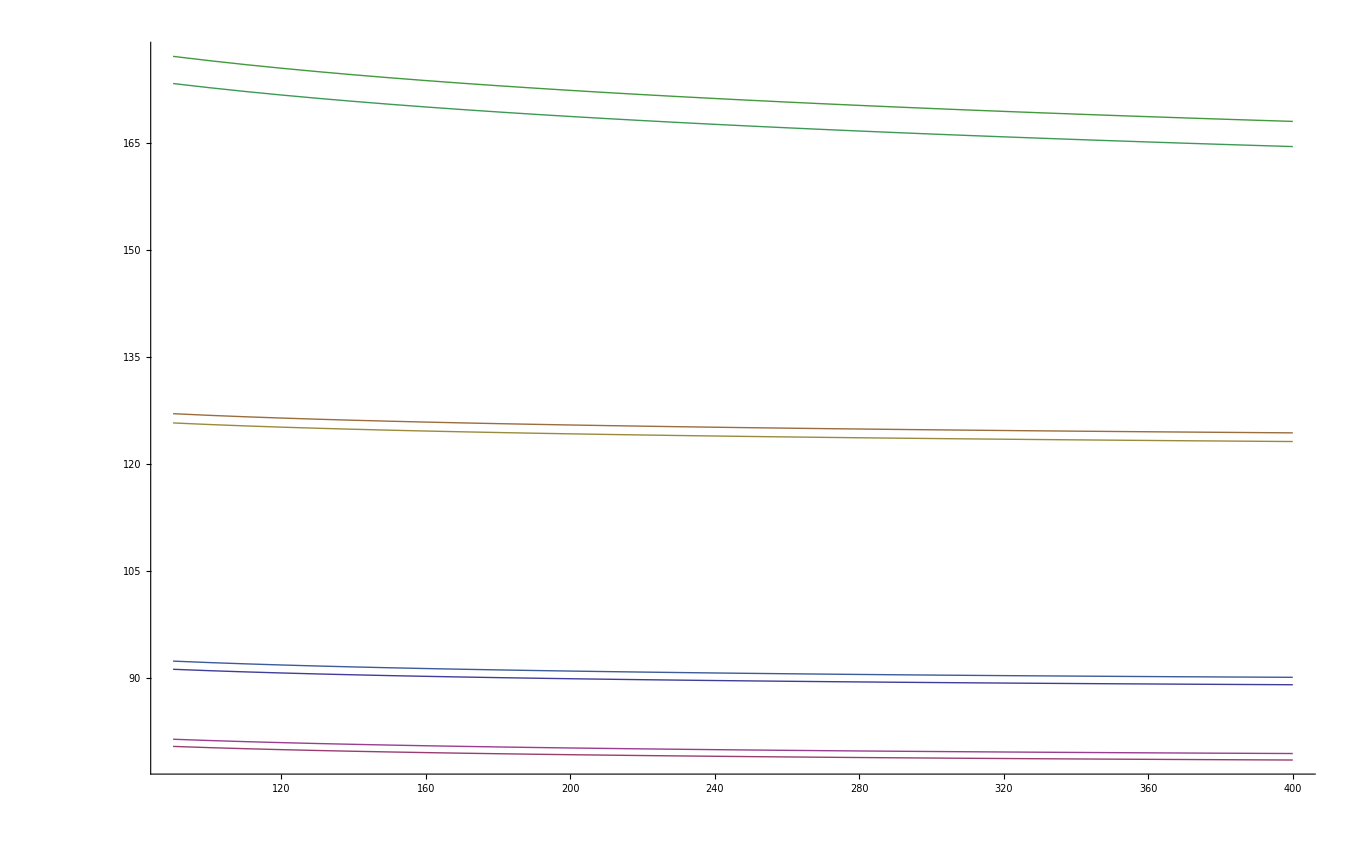

```mathematica
ListPlot[Join[sol91,sol172],Joined->True]
```

```mathematica
ScaleDependence[MZ]
```

```mathematica
k
```

```mathematica
ListPlot
```

### Difference between implicit and explicit determination of running parameters

```mathematica
Differe[scale_]:= Module[{pars = {g1,g2,gs,yt,lam,m, m/Sqrt[2 lam]},soli = sol2loopMT[scale][],sole1,sole2},sole1 = RunParsFromPoleMassesAndGfalpha[][scale];sole2 = RunParsFromPoleMassesAndGf[][scale];1-(pars /. soli)/(pars /. sole1)(* soli = Last /@ soli; sole = Last /@ Delete[sole/. z_ corr[___,x_]:> x,{{4},{8}}];Most[(1-soli/sole)]*)]
```

```mathematica
Differe[PDG`MT]
```

DEBUG: 1/aewSol = 127.756

{-0.00304485,-0.00173829,1.11022×10^-16,-0.0269879,-0.00751761,-0.00458869,-0.000833798}

{-0.00322733,1.11022×10^-16,1.11022×10^-16,-0.0306083,-0.00802591,-0.00529827,-0.00128818}

```mathematica
OverAllDiff[scale_]:= Plus @@ Map[#^2 &,Differe[scale]]
```

```mathematica
scales = Table[10+5i,{i,0,58}];
```

```mathematica
scales = Table[90+2i,{i,0,105}]
```

{90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254,256,258,260,262,264,266,268,270,272,274,276,278,280,282,284,286,288,290,292,294,296,298,300}

```mathematica
scales = Table[50+10i,{i,0,25}]
```

{50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300}

```mathematica
scales = Table[10.0  10^(i /20),{i,0,40}]
```

{10.,11.2202,12.5893,14.1254,15.8489,17.7828,19.9526,22.3872,25.1189,28.1838,31.6228,35.4813,39.8107,44.6684,50.1187,56.2341,63.0957,70.7946,79.4328,89.1251,100.,112.202,125.893,141.254,158.489,177.828,199.526,223.872,251.189,281.838,316.228,354.813,398.107,446.684,501.187,562.341,630.957,707.946,794.328,891.251,1000.}

```mathematica
scales
```

{10.,11.2202,12.5893,14.1254,15.8489,17.7828,19.9526,22.3872,25.1189,28.1838,31.6228,35.4813,39.8107,44.6684,50.1187,56.2341,63.0957,70.7946,79.4328,89.1251,100.,112.202,125.893,141.254,158.489,177.828,199.526,223.872,251.189,281.838,316.228,354.813,398.107,446.684,501.187,562.341,630.957,707.946,794.328,891.251,1000.}

```mathematica
sslog = {#,Differe[#]}& /@ scales;
```

DEBUG: 1/aewSol = 128.213

--->128.213

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.356

DEBUG:{10.98199596552403018 aEWtree$11835,aEWtree$11835 (701.7604446239217804 aEWtree$11835-182.1068184384063934 aQCD[90]),-8.869158509088928034 aEWtree$11835,aEWtree$11835 (2709.202445745490332 aEWtree$11835+26.40338204773840912 aQCD[90])}

DEBUG: 1/aewGF = 128.135

DEBUG: 1/aewSol = 128.197

--->128.197

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.343

DEBUG:{10.5828516480664979 aEWtree$11841,aEWtree$11841 (748.9211711672601957 aEWtree$11841-180.0828544441263547 aQCD[92]),-9.493660425156124455 aEWtree$11841,aEWtree$11841 (2762.390844324349647 aEWtree$11841+28.76991562441410091 aQCD[92])}

DEBUG: 1/aewGF = 128.121

DEBUG: 1/aewSol = 128.182

--->128.182

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.331

DEBUG:{10.19229174834726979 aEWtree$11847,aEWtree$11847 (795.8433582751237167 aEWtree$11847-178.1024199494640457 aQCD[94]),-10.10473114580999152 aEWtree$11847,aEWtree$11847 (2815.38520433483081 aEWtree$11847+31.08555203952349086 aQCD[94])}

DEBUG: 1/aewGF = 128.107

DEBUG: 1/aewSol = 128.167

--->128.167

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.319

DEBUG:{9.809954776270107608 aEWtree$11853,aEWtree$11853 (842.520889391411471 aEWtree$11853-176.1636819258454018 aQCD[96]),-10.70293625910443898 aEWtree$11853,aEWtree$11853 (2868.173907400287749 aEWtree$11853+33.35243457411297481 aQCD[96])}

DEBUG: 1/aewGF = 128.093

DEBUG: 1/aewSol = 128.153

--->128.153

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.307

DEBUG:{9.435501605222872845 aEWtree$11859,aEWtree$11859 (888.9486860607430432 aEWtree$11859-174.264920744498448 aQCD[98]),-11.2888063631459836 aEWtree$11859,aEWtree$11859 (2920.746861701731554 aEWtree$11859+35.57257391574409111 aQCD[98])}

DEBUG: 1/aewGF = 128.08

DEBUG: 1/aewSol = 128.139

--->128.139

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.295

DEBUG:{9.06861366460673734 aEWtree$11865,aEWtree$11865 (935.1225844387618921 aEWtree$11865-172.4045210112074479 aQCD[100]),-11.8628398940657928 aEWtree$11865,aEWtree$11865 (2973.095330123258139 aEWtree$11865+37.74785887501915607 aQCD[100])}

DEBUG: 1/aewGF = 128.068

DEBUG: 1/aewSol = 128.125

--->128.125

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.284

DEBUG:{8.708991311359860306 aEWtree$11871,aEWtree$11871 (981.0392271372550838 aEWtree$11871-170.5809633087045719 aQCD[102]),-12.42550567393666366 aEWtree$11871,aEWtree$11871 (3025.211779219035533 aEWtree$11871+39.88006604084561395 aQCD[102])}

DEBUG: 1/aewGF = 128.055

DEBUG: 1/aewSol = 128.111

--->128.111

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.272

DEBUG:{8.356352359616928976 aEWtree$11877,aEWtree$11877 (1026.695968318399357 aEWtree$11877-168.7928167409301542 aQCD[104]),-12.977245211270349 aEWtree$11877,aEWtree$11877 (3077.08974620968498 aEWtree$11877+41.97086849811010288 aQCD[104])}

DEBUG: 1/aewGF = 128.044

DEBUG: 1/aewSol = 128.098

--->128.098

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.261

DEBUG:{8.010430750427829287 aEWtree$11883,aEWtree$11883 (1072.0907902644251 aEWtree$11883-167.0387321874988241 aQCD[106]),-13.51847478237811085 aEWtree$11883,aEWtree$11883 (3128.723721629749973 aEWtree$11883+44.02184371493951699 aQCD[106])}

DEBUG: 1/aewGF = 128.032

DEBUG: 1/aewSol = 128.085

--->128.085

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.251

DEBUG:{7.670975345824483906 aEWtree$11889,aEWtree$11889 (1117.222229909935561 aEWtree$11889-165.317436188705022 aQCD[108]),-14.04958731817591717 aEWtree$11889,aEWtree$11889 (3180.109045594580515 aEWtree$11889+46.03448069269962485 aQCD[108])}

DEBUG: 1/aewGF = 128.021

DEBUG: 1/aewSol = 128.072

--->128.072

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.24

DEBUG:{7.337748833543301597 aEWtree$11895,aEWtree$11895 (1162.089314043068666 aEWtree$11895-163.6277253916362749 aQCD[110]),-14.57095411785766088 aEWtree$11895,aEWtree$11895 (3231.241815945680481 aEWtree$11895+48.01018645991465265 aQCD[110])}

DEBUG: 1/aewGF = 128.01

DEBUG: 1/aewSol = 128.059

--->128.059

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.23

DEBUG:{7.010526730438070674 aEWtree$11901,aEWtree$11901 (1206.69150206600663 aEWtree$11901-161.968461496721767 aQCD[112]),-15.08292640815713826 aEWtree$11901,aEWtree$11901 (3282.118806779698421 aEWtree$11901+49.95029198104951332 aQCD[112])}

DEBUG: 1/aewGF = 127.999

DEBUG: 1/aewSol = 128.047

--->128.047

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.22

DEBUG:{6.689096474100869994 aEWtree$11907,aEWtree$11907 (1251.028635360948182 aEWtree$11907-160.338566651562372 aQCD[114]),-15.58583676459960322 aEWtree$11907,aEWtree$11907 (3332.737396073036125 aEWtree$11907+51.85605754230516901 aQCD[114])}

DEBUG: 1/aewGF = 127.989

DEBUG: 1/aewSol = 128.035

--->128.035

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.21

DEBUG:{6.373256593484967163 aEWtree$11913,aEWtree$11913 (1295.100892439430524 aEWtree$11913-158.7370192453605859 aQCD[116]),-16.08000040914667105 aEWtree$11913,aEWtree$11913 (3383.09550129038486 aEWtree$11913+53.72867766900984604 aQCD[116])}

DEBUG: 1/aewGF = 127.979

DEBUG: 1/aewSol = 128.023

--->128.023

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.2

DEBUG:{6.06281595042547794 aEWtree$11919,aEWtree$11919 (1338.908749164784452 aEWtree$11919-157.1628500628558175 aQCD[118]),-16.56571639691445608 aEWtree$11919,aEWtree$11919 (3433.191522014969742 aEWtree$11919+55.56928562265618835 aQCD[118])}

DEBUG: 1/aewGF = 127.969

DEBUG: 1/aewSol = 128.011

--->128.011

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.19

DEBUG:{5.75759304490719106 aEWtree$11925,aEWtree$11925 (1382.452943432770685 aEWtree$11925-155.6151387615060786 aQCD[120]),-17.04326870315278193 aEWtree$11925,aEWtree$11925 (3483.024288765838108 aEWtree$11925+57.37895751998037013 aQCD[120])}

DEBUG: 1/aewGF = 127.959

DEBUG: 1/aewSol = 127.999

--->127.999

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.181

DEBUG:{5.457415377756463841 aEWtree$11931,aEWtree$11931 (1425.73444377677936 aEWtree$11931-154.0930106398532109 aQCD[122]),-17.51292722037858632 aEWtree$11931,aEWtree$11931 (3532.593017276558348 aEWtree$11931+59.15871611157289035 aQCD[122])}

DEBUG: 1/aewGF = 127.95

DEBUG: 1/aewSol = 127.988

--->127.988

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.172

DEBUG:{5.162118865153930958 aEWtree$11937,aEWtree$11937 (1468.754421433561912 aEWtree$11937-152.5956336686588804 aQCD[124]),-17.97494867443038748 aEWtree$11937,aEWtree$11937 (3581.897267603136564 aEWtree$11937+60.90953425324287349 aQCD[124])}

DEBUG: 1/aewGF = 127.941

DEBUG: 1/aewSol = 127.977

--->127.977

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.163

DEBUG:{4.871547299992446959 aEWtree$11943,aEWtree$11943 (1511.514225465179974 aEWtree$11943-151.1222157595813896 aQCD[126]),-18.42957746722861667 aEWtree$11943,aEWtree$11943 (3630.936907509246733 aEWtree$11943+62.6323380996361619 aQCD[126])}

DEBUG: 1/aewGF = 127.932

DEBUG: 1/aewSol = 127.966

--->127.966

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.154

DEBUG:{4.585551855653268483 aEWtree$11949,aEWtree$11949 (1554.01536058417929 aEWtree$11949-149.6720022489450892 aQCD[128]),-18.87704645316829287 aEWtree$11949,aEWtree$11949 (3679.712079645996086 aEWtree$11949+64.32801004635493411 aQCD[128])}

DEBUG: 1/aewGF = 127.923

DEBUG: 1/aewSol = 127.955

--->127.955

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.145

DEBUG:{4.30399062825401242 aEWtree$11955,aEWtree$11955 (1596.259467373250342 aEWtree$11955-148.244273576590833 aQCD[130]),-19.3175776553186917 aEWtree$11955,aEWtree$11955 (3728.22317210307777 aEWtree$11955+65.99739144397749677 aQCD[130])}

DEBUG: 1/aewGF = 127.915

DEBUG: 1/aewSol = 127.944

--->127.944

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.136

DEBUG:{4.026728213843755318 aEWtree$11961,aEWtree$11961 (1638.24830462882495 aEWtree$11961-146.8383431419349075 aQCD[132]),-19.7513829269446502 aEWtree$11961,aEWtree$11961 (3776.470791959799291 aEWtree$11961+67.6412851048758651 aQCD[132])}

DEBUG: 1/aewGF = 127.907

DEBUG: 1/aewSol = 127.934

--->127.934

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.128

DEBUG:{3.753635317391712386 aEWtree$11967,aEWtree$11967 (1679.98373359114755 aEWtree$11967-145.453555321245489 aQCD[134]),-20.17866456328358412 aEWtree$11967,aEWtree$11967 (3824.455741509190336 aEWtree$11967+69.26045762152866661 aQCD[134])}

DEBUG: 1/aewGF = 127.899

DEBUG: 1/aewSol = 127.924

--->127.924

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.119

DEBUG:{3.484588390743021179 aEWtree$11973,aEWtree$11973 (1721.467703852008776 aEWtree$11973-144.089283631804261 aQCD[136]),-20.59961586800051767 aEWtree$11973,aEWtree$11973 (3872.178996867207147 aEWtree$11973+70.85564151308757204 aQCD[136])}

DEBUG: 1/aewGF = 127.891

DEBUG: 1/aewSol = 127.913

--->127.913

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.111

DEBUG:{3.219469297004035079 aEWtree$11979,aEWtree$11979 (1762.702240756261861 aEWtree$11979-142.7449290300856642 aQCD[138]),-21.01442167829145689 aEWtree$11979,aEWtree$11979 (3919.641688712935654 aEWtree$11979+72.4275372152427087 aQCD[138])}

DEBUG: 1/aewGF = 127.883

DEBUG: 1/aewSol = 127.904

--->127.904

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.103

DEBUG:{2.958164999075154115 aEWtree$11985,aEWtree$11985 (1803.689434134923852 aEWtree$11985-141.419918332382448 aQCD[140]),-21.42325885220548131 aEWtree$11985,aEWtree$11985 (3966.84508493505238 aEWtree$11985+73.97681492691690605 aQCD[140])}

DEBUG: 1/aewGF = 127.876

DEBUG: 1/aewSol = 127.894

--->127.894

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.095

DEBUG:{2.700567270275831306 aEWtree$11991,aEWtree$11991 (1844.431428226574671 aEWtree$11991-140.1137027474552862 aQCD[142]),-21.82629672140138009 aEWtree$11991,aEWtree$11991 (4013.790574985701202 aEWtree$11991+75.50411632597504721 aQCD[142])}

DEBUG: 1/aewGF = 127.868

DEBUG: 1/aewSol = 127.884

--->127.884

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.087

DEBUG:{2.446572425207644779 aEWtree$11997,aEWtree$11997 (1884.93041266030696 aEWtree$11997-138.825756511804713 aQCD[144]),-22.22369751223977131 aEWtree$11997,aEWtree$11997 (4060.4796557653364 aEWtree$11997+77.01005616494158119 aQCD[144])}

DEBUG: 1/aewGF = 127.861

DEBUG: 1/aewSol = 127.874

--->127.874

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.079

DEBUG:{2.196081069180367143 aEWtree$12003,aEWtree$12003 (1925.188614387917021 aEWtree$12003-137.5555756190715139 aQCD[146]),-22.6156167378315251 aEWtree$12003,aEWtree$12003 (4106.91391888192252 aEWtree$12003+78.4952237566577001 aQCD[146])}

DEBUG: 1/aewGF = 127.854

DEBUG: 1/aewSol = 127.865

--->127.865

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.071

DEBUG:{1.948997864685514684 aEWtree$12009,aEWtree$12009 (1965.20829046573095 aEWtree$12009-136.302676635880752 aQCD[148]),-23.00220356341366737 aEWtree$12009,aEWtree$12009 (4153.095039145196685 aEWtree$12009+79.96018435886371233 aQCD[148])}

DEBUG: 1/aewGF = 127.847

DEBUG: 1/aewSol = 127.856

--->127.856

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.064

DEBUG:{1.705231313544274507 aEWtree$12015,aEWtree$12015 (2004.99172159757419 aEWtree$12015-135.0665955971667608 aQCD[150]),-23.383601147201125 aEWtree$12015,aEWtree$12015 (4199.024764171961397 aEWtree$12015+81.4054804658477617 aQCD[150])}

DEBUG: 1/aewGF = 127.84

DEBUG: 1/aewSol = 127.846

--->127.846

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.056

DEBUG:{1.464693553484030869 aEWtree$12021,aEWtree$12021 (2044.541206360188264 aEWtree$12021-133.8468869746620644 aQCD[152]),-23.75994695866345723 aEWtree$12021,aEWtree$12021 (4244.704904991820669 aEWtree$12021+82.83163301454712485 aQCD[152])}

DEBUG: 1/aewGF = 127.834

DEBUG: 1/aewSol = 127.837

--->127.837

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.049

DEBUG:{1.227300168011718373 aEWtree$12027,aEWtree$12027 (2083.859056041014889 aEWtree$12027-132.6431227128112783 aQCD[154]),-24.13137307599734951 aEWtree$12027,aEWtree$12027 (4290.137327554609996 aEWtree$12027+84.23914251181239979 aQCD[154])}

DEBUG: 1/aewGF = 127.827

DEBUG: 1/aewSol = 127.828

--->127.828

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.042

DEBUG:{0.9929700085544661396 aEWtree$12033,aEWtree$12033 (2122.947590025875334 aEWtree$12033-131.4548913268894688 aQCD[156]),-24.49800646440568081 aEWtree$12033,aEWtree$12033 (4335.323945051280425 aEWtree$12033+85.62849008893870702 aQCD[156])}

DEBUG: 1/aewGF = 127.821

DEBUG: 1/aewSol = 127.82

--->127.82

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.035

DEBUG:{0.7616250279298133322 aEWtree$12039,aEWtree$12039 (2161.809131680787324 aEWtree$12039-130.2817970585700187 aQCD[158]),-24.85996923665032366 aEWtree$12039,aEWtree$12039 (4380.266710969242649 aEWtree$12039+87.00013848902366791 aQCD[158])}

DEBUG: 1/aewGF = 127.815

DEBUG: 1/aewSol = 127.811

--->127.811

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.028

DEBUG:{0.5331901242903519271 aEWtree$12045,aEWtree$12045 (2200.446004678095311 aEWtree$12045-129.1234590846057728 aQCD[160]),-25.21737889721663593 aEWtree$12045,aEWtree$12045 (4424.967612811387889 aEWtree$12045+88.354532992222324 aQCD[160])}

DEBUG: 1/aewGF = 127.809

DEBUG: 1/aewSol = 127.802

--->127.802

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.021

DEBUG:{0.307592994762021075 aEWtree$12051,aEWtree$12051 (2238.860529722361598 aEWtree$12051-127.9795107746643384 aQCD[162]),-25.57034857131124952 aEWtree$12051,aEWtree$12051 (4469.428666415337411 aEWtree$12051+89.6921022835282278 aQCD[162])}

DEBUG: 1/aewGF = 127.803

DEBUG: 1/aewSol = 127.794

--->127.794

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.014

DEBUG:{0.0847639980623448156 aEWtree$12057,aEWtree$12057 (2277.05502163612036 aEWtree$12057-126.8495989946984998 aQCD[164]),-25.91898721980982114 aEWtree$12057,aEWtree$12057 (4513.651910815898106 aEWtree$12057+91.0132592673122872 aQCD[164])}

DEBUG: 1/aewGF = 127.797

DEBUG: 1/aewSol = 127.786

--->127.786

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.007

DEBUG:{-0.135363974554531669 aEWtree$12063,aEWtree$12063 (2315.031786769744546 aEWtree$12063-125.7333834525398089 aQCD[166]),-26.26339984117666087 aEWtree$12063,aEWtree$12063 (4557.639403599484318 aEWtree$12063+92.31840183249188933 aQCD[166])}

DEBUG: 1/aewGF = 127.791

DEBUG: 1/aewSol = 127.777

--->127.777

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.

DEBUG:{-0.3528556206243921665 aEWtree$12069,aEWtree$12069 (2352.793120703349562 aEWtree$12069-124.630536082681085 aQCD[168]),-26.60368766129247068 aEWtree$12069,aEWtree$12069 (4601.39321670441133 aEWtree$12069+93.60791357187811518 aQCD[168])}

DEBUG: 1/aewGF = 127.786

DEBUG: 1/aewSol = 127.769

--->127.769

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.994

DEBUG:{-0.5677733406198953829 aEWtree$12075,aEWtree$12075 (2390.341306211949343 aEWtree$12075-123.5407404674649463 aQCD[170]),-26.93994831204886072 aEWtree$12075,aEWtree$12075 (4644.915432625533633 aEWtree$12075+94.88216445895496129 aQCD[170])}

DEBUG: 1/aewGF = 127.78

DEBUG: 1/aewSol = 127.761

--->127.761

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.987

DEBUG:{-0.7801773454217904298 aEWtree$12081,aEWtree$12081 (2427.678611467980828 aEWtree$12081-122.4636912921233493 aQCD[172]),-27.27227599949800681 aEWtree$12081,aEWtree$12081 (4688.208140985786464 aEWtree$12081+96.1415114850780394 aQCD[172])}

DEBUG: 1/aewGF = 127.775

DEBUG: 1/aewSol = 127.753

--->127.753

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.981

DEBUG:{-0.990125757577495665 aEWtree$12087,aEWtree$12087 (2464.807288457924583 aEWtree$12087-121.3990938313199051 aQCD[174]),-27.60076166228200325 aEWtree$12087,aEWtree$12087 (4731.273435440840864 aEWtree$12087+97.38629925983844687 aQCD[174])}

DEBUG: 1/aewGF = 127.77

DEBUG: 1/aewSol = 127.745

--->127.745

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.974

DEBUG:{-1.197674706773083809 aEWtree$12093,aEWtree$12093 (2501.729571592102851 aEWtree$12093-120.3466634650346045 aQCD[176]),-27.92549312100850418 aEWtree$12093,aEWtree$12093 (4774.113410886394561 aEWtree$12093+98.61686057711781753 aQCD[176])}

DEBUG: 1/aewGF = 127.765

DEBUG: 1/aewSol = 127.737

--->127.737

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.968

DEBUG:{-1.402878419911015128 aEWtree$12099,aEWtree$12099 (2538.447676488758873 aEWtree$12099-119.306125221801487 aQCD[178]),-28.24655521918650524 aEWtree$12099,aEWtree$12099 (4816.730160940455683 aEWtree$12099+99.833516949160768 aQCD[178])}

DEBUG: 1/aewGF = 127.759

DEBUG: 1/aewSol = 127.73

--->127.73

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.962

DEBUG:{-1.60578930615527177 aEWtree$12105,aEWtree$12105 (2574.963798915417439 aEWtree$12105-118.2772133474653994 aQCD[180]),-28.56402995628811436 aEWtree$12105,aEWtree$12105 (4859.125775675725276 aEWtree$12105+101.0365791108089696 aQCD[180])}

DEBUG: 1/aewGF = 127.754

DEBUG: 1/aewSol = 127.722

--->127.722

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.955

DEBUG:{-1.806458037277570803 aEWtree$12111,aEWtree$12111 (2611.280113872205448 aEWtree$12111-117.2596708977658423 aQCD[182]),-28.87799661345838028 aEWtree$12111,aEWtree$12111 (4901.302339579470878 aEWtree$12111+102.2263474958752396 aQCD[182])}

DEBUG: 1/aewGF = 127.75

DEBUG: 1/aewSol = 127.715

--->127.715

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.949

DEBUG:{-2.00493362361280405 aEWtree$12117,aEWtree$12117 (2647.398774803274232 aEWtree$12117-116.2532493531853624 aQCD[184]),-29.18853187235531082 aEWtree$12117,aEWtree$12117 (4943.261929720384899 aEWtree$12117+103.4031126874846601 aQCD[184])}

DEBUG: 1/aewGF = 127.745

DEBUG: 1/aewSol = 127.707

--->127.707

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.943

DEBUG:{-2.201263485908531865 aEWtree$12123,aEWtree$12123 (2683.32191292382285 aEWtree$12123-115.2577082546182025 aQCD[186]),-29.49570992756571983 aEWtree$12123,aEWtree$12123 (4985.006614103912082 aEWtree$12123+104.5671558440714723 aQCD[186])}

DEBUG: 1/aewGF = 127.74

DEBUG: 1/aewSol = 127.7

--->127.7

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.937

DEBUG:{-2.395493523332032166 aEWtree$12129,aEWtree$12129 (2719.051636651419573 aEWtree$12129-114.272814858523055 aQCD[188]),-29.79960259300917784 aEWtree$12129,aEWtree$12129 (5026.538450199160369 aEWtree$12129+105.7187491025940488 aQCD[188])}

DEBUG: 1/aewGF = 127.735

DEBUG: 1/aewSol = 127.692

--->127.692

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.931

DEBUG:{-2.587668177878885674 aEWtree$12135,aEWtree$12135 (2754.590031131405409 aEWtree$12135-113.298343810322752 aQCD[190]),-30.10027940271180042 aEWtree$12135,aEWtree$12135 (5067.859483622132657 aEWtree$12135+106.8581559604145124 aQCD[190])}

DEBUG: 1/aewGF = 127.731

DEBUG: 1/aewSol = 127.685

--->127.685

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.926

DEBUG:{-2.777830495409194347 aEWtree$12141,aEWtree$12141 (2789.939157847134009 aEWtree$12141-112.3340768349044126 aQCD[192]),-30.39780770630362532 aEWtree$12141,aEWtree$12141 (5108.971746961327057 aEWtree$12141+107.9856316371835323 aQCD[192])}

DEBUG: 1/aewGF = 127.726

DEBUG: 1/aewSol = 127.678

--->127.678

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.92

DEBUG:{-2.966022183521126716 aEWtree$12147,aEWtree$12147 (2825.101054306681706 aEWtree$12147-111.3798024431567323 aQCD[194]),-30.69225275956766542 aEWtree$12147,aEWtree$12147 (5149.877258733123124 aEWtree$12147+109.1014234179735778 aQCD[194])}

DEBUG: 1/aewGF = 127.722

DEBUG: 1/aewSol = 127.671

--->127.671

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.914

DEBUG:{-3.152283666456429105 aEWtree$12153,aEWtree$12153 (2860.07773379844902 aEWtree$12153-110.4353156535574598 aQCD[196]),-30.98367781034517 aEWtree$12153,aEWtree$12153 (5190.578022455415443 aEWtree$12153+110.205770978814647 aQCD[196])}

DEBUG: 1/aewGF = 127.718

DEBUG: 1/aewSol = 127.664

--->127.664

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.908

DEBUG:{-3.33665413721870751 aEWtree$12159,aEWtree$12159 (2894.871185208791034 aEWtree$12159-109.5004177278942324 aQCD[198]),-31.27214418007998259 aEWtree$12159,aEWtree$12159 (5231.076025829025053 aEWtree$12159+111.2989066957044619 aQCD[198])}

DEBUG: 1/aewGF = 127.714

DEBUG: 1/aewSol = 127.657

--->127.657

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.903

DEBUG:{-3.519171607072564612 aEWtree$12165,aEWtree$12165 (2929.483372895451129 aEWtree$12165-108.5749159202664617 aQCD[200]),-31.55771134126497899 aEWtree$12165,aEWtree$12165 (5271.373240017362019 aEWtree$12165+112.3810559380897111 aQCD[200])}

DEBUG: 1/aewGF = 127.709

DEBUG: 1/aewSol = 127.65

--->127.65

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.897

DEBUG:{-3.699872952579968208 aEWtree$12171,aEWtree$12171 (2963.916236611160288 aEWtree$12171-107.6586232385753227 aQCD[202]),-31.84043699103525476 aEWtree$12171,aEWtree$12171 (5311.471619015660593 aEWtree$12171+113.452437347745492 aQCD[202])}

DEBUG: 1/aewGF = 127.705

DEBUG: 1/aewSol = 127.644

--->127.644

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.892

DEBUG:{-3.878793960319441652 aEWtree$12177,aEWtree$12177 (2998.171691472283904 aEWtree$12177-106.7513582177635871 aQCD[204]),-32.12037712113585002 aEWtree$12177,aEWtree$12177 (5351.37309910180889 aEWtree$12177+114.5132631039161676 aQCD[204])}

DEBUG: 1/aewGF = 127.701

DEBUG: 1/aewSol = 127.637

--->127.637

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.886

DEBUG:{-4.055969369423724137 aEWtree$12183,aEWtree$12183 (3032.251627967878103 aEWtree$12183-105.8529447041174692 aQCD[206]),-32.39758608447624956 aEWtree$12183,aEWtree$12183 (5391.079598361585614 aEWtree$12183+115.5637391755218909 aQCD[206])}

DEBUG: 1/aewGF = 127.697

DEBUG: 1/aewSol = 127.63

--->127.63

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.881

DEBUG:{-4.231432912062372981 aEWtree$12189,aEWtree$12189 (3066.157912004938077 aEWtree$12189-104.9632116499891708 aQCD[208]),-32.67211665846953493 aEWtree$12189,aEWtree$12189 (5430.593016281712696 aEWtree$12189+116.6040655611806558 aQCD[208])}

DEBUG: 1/aewGF = 127.694

DEBUG: 1/aewSol = 127.624

--->127.624

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.876

DEBUG:{-4.4052173519873087 aEWtree$12195,aEWtree$12195 (3099.892384986020044 aEWtree$12195-104.0819929183417751 aQCD[210]),-32.94402010534081374 aEWtree$12195,aEWtree$12195 (5469.915233404628228 aEWtree$12195+117.6344365177455 aQCD[210])}

DEBUG: 1/aewGF = 127.69

DEBUG: 1/aewSol = 127.617

--->127.617

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.871

DEBUG:{-4.577354521251472671 aEWtree$12201,aEWtree$12201 (3133.456863915766878 aEWtree$12201-103.209127096557842 aQCD[212]),-33.21334622957729719 aEWtree$12201,aEWtree$12201 (5509.048111039547745 aEWtree$12201+118.6550407780100688 aQCD[212])}

DEBUG: 1/aewGF = 127.686

DEBUG: 1/aewSol = 127.611

--->127.611

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.865

DEBUG:{-4.747875355203526336 aEWtree$12207,aEWtree$12207 (3166.853141533181975 aEWtree$12207-102.3444573189897775 aQCD[214]),-33.48014343268106939 aEWtree$12207,aEWtree$12207 (5547.99349102473794 aEWtree$12207+119.6660617581927838 aQCD[214])}

DEBUG: 1/aewGF = 127.682

DEBUG: 1/aewSol = 127.604

--->127.604

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.86

DEBUG:{-4.916809925854818049 aEWtree$12213,aEWtree$12213 (3200.082986466795376 aEWtree$12213-101.4878310977640415 aQCD[216]),-33.74445876537510352 aEWtree$12213,aEWtree$12213 (5586.753195536412839 aEWtree$12213+120.6676777557701757 aQCD[216])}

DEBUG: 1/aewGF = 127.679

DEBUG: 1/aewSol = 127.598

--->127.598

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.855

DEBUG:{-5.084187473708634606 aEWtree$12219,aEWtree$12219 (3233.148143410120138 aEWtree$12219-100.6391001613827358 aQCD[218]),-34.00633797740336631 aEWtree$12219,aEWtree$12219 (5625.329026940024402 aEWtree$12219+121.6600621381930648 aQCD[218])}

DEBUG: 1/aewGF = 127.675

DEBUG: 1/aewSol = 127.592

--->127.592

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.85

DEBUG:{-5.250036438136000356 aEWtree$12225,aEWtree$12225 (3266.050333315041887 aEWtree$12225-99.7981203006952956 aQCD[220]),-34.26582556505684723 aEWtree$12225,aEWtree$12225 (5663.722767680134187 aEWtree$12225+122.6433835229852025 aQCD[220])}

DEBUG: 1/aewGF = 127.672

DEBUG: 1/aewSol = 127.586

--->127.586

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.845

DEBUG:{-5.414384486376948141 aEWtree$12231,aEWtree$12231 (3298.79125360099693 aEWtree$12231-98.96475122184008144 aQCD[222]),-34.5229648165489997 aEWtree$12231,aEWtree$12231 (5701.936180205299117 aEWtree$12231+123.6178059496923058 aQCD[222])}

DEBUG: 1/aewGF = 127.668

DEBUG: 1/aewSol = 127.58

--->127.58

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.84

DEBUG:{-5.577258541241231284 aEWtree$12237,aEWtree$12237 (3331.372578377997577 aEWtree$12237-98.1388564057807892 aQCD[224]),-34.7777978553563246 aEWtree$12237,aEWtree$12237 (5739.971006924787258 aEWtree$12237+124.5834890441200622 aQCD[224])}

DEBUG: 1/aewGF = 127.665

DEBUG: 1/aewSol = 127.573

--->127.573

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.835

DEBUG:{-5.738684807577843098 aEWtree$12243,aEWtree$12243 (3363.795958681732362 aEWtree$12243-97.3203029740859388 aQCD[226]),-35.03036568163262787 aEWtree$12243,aEWtree$12243 (5777.828970194118583 aEWtree$12243+125.5405881752723691 aQCD[226])}

DEBUG: 1/aewGF = 127.661

DEBUG: 1/aewSol = 127.567

--->127.567

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.83

DEBUG:{-5.898688797578431961 aEWtree$12249,aEWtree$12249 (3396.063022719144812 aEWtree$12249-96.5089615606213951 aQCD[228]),-35.28070821179878958 aEWtree$12249,aEWtree$12249 (5815.511772326759896 aEWtree$12249+126.4892546053757174 aQCD[228])}

DEBUG: 1/aewGF = 127.658

DEBUG: 1/aewSol = 127.561

--->127.561

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.826

DEBUG:{-6.057295354975720595 aEWtree$12255,aEWtree$12255 (3428.175376123029545 aEWtree$12255-95.70470618884605447 aQCD[230]),-35.52886431640365386 aEWtree$12255,aEWtree$12255 (5853.021095629505865 aEWtree$12255+127.4296356333520442 aQCD[230])}

DEBUG: 1/aewGF = 127.655

DEBUG: 1/aewSol = 127.556

--->127.556

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.821

DEBUG:{-6.214528678194334791 aEWtree$12261,aEWtree$12261 (3460.134602214332456 aEWtree$12261-94.90741415441961039 aQCD[232]),-35.77487185634585738 aEWtree$12261,aEWtree$12261 (5890.358602459228393 aEWtree$12261+128.3618747320803933 aQCD[232])}

DEBUG: 1/aewGF = 127.652

DEBUG: 1/aewSol = 127.55

--->127.55

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.816

DEBUG:{-6.370412342507996681 aEWtree$12267,aEWtree$12267 (3491.942262270952305 aEWtree$12267-94.11696591284880042 aQCD[234]),-36.01876771754101313 aEWtree$12267,aEWtree$12267 (5927.525935298943011 aEWtree$12267+129.2861116797672985 aQCD[234])}

DEBUG: 1/aewGF = 127.649

DEBUG: 1/aewSol = 127.544

--->127.544

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.811

DEBUG:{-6.524969321253823998 aEWtree$12273,aEWtree$12273 (3523.599895801963343 aEWtree$12273-93.33324497191484337 aQCD[236]),-36.26058784411364239 aEWtree$12273,aEWtree$12273 (5964.524716851307559 aEWtree$12273+130.2024826857267349 aQCD[236])}

DEBUG: 1/aewGF = 127.646

DEBUG: 1/aewSol = 127.538

--->127.538

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.807

DEBUG:{-6.67822200615147859 aEWtree$12279,aEWtree$12279 (3555.109020826271092 aEWtree$12279-92.55613778863996499 aQCD[238]),-36.5003672701885494 aEWtree$12279,aEWtree$12279 (6001.3565501477291 aEWtree$12279+131.1111205108526974 aQCD[238])}

DEBUG: 1/aewGF = 127.643

DEBUG: 1/aewSol = 127.532

--->127.532

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.802

DEBUG:{-6.830192226772110896 aEWtree$12285,aEWtree$12285 (3586.471134154820259 aEWtree$12285-91.78553367056510576 aQCD[240]),-36.73814015035196828 aEWtree$12285,aEWtree$12285 (6038.02301867157195 aEWtree$12285+132.0121545830509154 aQCD[240])}

DEBUG: 1/aewGF = 127.64

DEBUG: 1/aewSol = 127.527

--->127.527

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.797

DEBUG:{-6.980901269199436092 aEWtree$12291,aEWtree$12291 (3617.687711675540498 aEWtree$12291-91.02132468112413025 aQCD[242]),-36.9739397888487155 aEWtree$12291,aEWtree$12291 (6074.52568649391775 aEWtree$12291+132.9057111078806935 aQCD[242])}

DEBUG: 1/aewGF = 127.637

DEBUG: 1/aewSol = 127.521

--->127.521

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.793

DEBUG:{-7.13036989392283813 aEWtree$12297,aEWtree$12297 (3648.760208640305783 aEWtree$12297-90.26340554891223907 aQCD[244]),-37.20779866757777265 aEWtree$12297,aEWtree$12297 (6110.866098420582507 aEWtree$12297+133.7919131746434353 aQCD[244])}

DEBUG: 1/aewGF = 127.634

DEBUG: 1/aewSol = 127.515

--->127.515

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.788

DEBUG:{-7.278618353000118019 aEWtree$12303,aEWtree$12303 (3679.690059953251927 aEWtree$12303-89.5116735806578338 aQCD[246]),-37.43974847294515346 aEWtree$12303,aEWtree$12303 (6147.045780149124035 aEWtree$12303+134.6708808581408775 aQCD[246])}

DEBUG: 1/aewGF = 127.631

DEBUG: 1/aewSol = 127.51

--->127.51

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.784

DEBUG:{-7.425666406525371005 aEWtree$12309,aEWtree$12309 (3710.47868045985941 aEWtree$12309-88.76602857771790971 aQCD[248]),-37.66982012162957383 aEWtree$12309,aEWtree$12309 (6183.066238434726927 aEWtree$12309+135.5427313163134174 aQCD[248])}

DEBUG: 1/aewGF = 127.628

DEBUG: 1/aewSol = 127.504

--->127.504

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.78

DEBUG:{-7.571533338435481167 aEWtree$12315,aEWtree$12315 (3741.12746523626195 aEWtree$12315-88.0263727559271558 aQCD[250]),-37.8980437853133222 aEWtree$12315,aEWtree$12315 (6218.928961263917039 aEWtree$12315+136.4075788839570939 aQCD[250])}

DEBUG: 1/aewGF = 127.625

DEBUG: 1/aewSol = 127.499

--->127.499

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.775

DEBUG:{-7.716237971686854992 aEWtree$12321,aEWtree$12321 (3771.637789878305476 aEWtree$12321-87.2926106686404204 aQCD[252]),-38.12444891442780302 aEWtree$12321,aEWtree$12321 (6254.635418035181854 aEWtree$12321+137.2655351627067047 aQCD[252])}

DEBUG: 1/aewGF = 127.623

DEBUG: 1/aewSol = 127.494

--->127.494

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.771

DEBUG:{-7.859798682832264809 aEWtree$12327,aEWtree$12327 (3802.011010789926225 aEWtree$12327-86.5646491328170748 aQCD[254]),-38.34906426096049333 aEWtree$12327,aEWtree$12327 (6290.187059745566753 aEWtree$12327+138.1167091074621613 aQCD[254])}

DEBUG: 1/aewGF = 127.62

DEBUG: 1/aewSol = 127.488

--->127.488

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.767

DEBUG:{-8.002233416026033471 aEWtree$12333,aEWtree$12333 (3832.248465470454243 aEWtree$12333-85.8423971580041209 aQCD[256]),-38.57191790036747923 aEWtree$12333,aEWtree$12333 (6325.585319182530185 aEWtree$12333+138.9612071094254764 aQCD[256])}

DEBUG: 1/aewGF = 127.617

DEBUG: 1/aewSol = 127.483

--->127.483

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.762

DEBUG:{-8.143559696484253253 aEWtree$12339,aEWtree$12339 (3862.351472800499399 aEWtree$12339-85.12576587808268551 aQCD[258]),-38.79303725263333903 aEWtree$12339,aEWtree$12339 (6360.831611120259979 aEWtree$12339+139.7991330759066279 aQCD[258])}

DEBUG: 1/aewGF = 127.615

DEBUG: 1/aewSol = 127.478

--->127.478

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.758

DEBUG:{-8.28379464342528953 aEWtree$12345,aEWtree$12345 (3892.321333326114179 aEWtree$12345-84.414668485649866 aQCD[260]),-39.01244910251787799 aEWtree$12345,aEWtree$12345 (6395.927332519825441 aEWtree$12345+140.6305885070480382 aQCD[260])}

DEBUG: 1/aewGF = 127.612

DEBUG: 1/aewSol = 127.472

--->127.472

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.754

DEBUG:{-8.422954982514464748 aEWtree$12351,aEWtree$12351 (3922.159329540948489 aEWtree$12351-83.7090201689147576 aQCD[262]),-39.23017961902710332 aEWtree$12351,aEWtree$12351 (6430.873862732525385 aEWtree$12351+141.455672569609312 aQCD[262])}

DEBUG: 1/aewGF = 127.61

DEBUG: 1/aewSol = 127.467

--->127.467

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.75

DEBUG:{-8.561057057835546624 aEWtree$12357,aEWtree$12357 (3951.866726166157559 aEWtree$12357-83.00873805099394143 aQCD[264]),-39.4462543741438365 aEWtree$12357,aEWtree$12357 (6465.672563705908431 aEWtree$12357+142.2744821679464055 aQCD[264])}

DEBUG: 1/aewGF = 127.607

DEBUG: 1/aewSol = 127.462

--->127.462

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.746

DEBUG:{-8.6981168434104689 aEWtree$12363,aEWtree$12363 (3981.44477042784403 aEWtree$12363-82.31374113149777459 aQCD[266]),-39.6606983608514889 aEWtree$12363,aEWtree$12363 (6500.324780191908427 aEWtree$12363+143.0871120123122455 aQCD[266])}

DEBUG: 1/aewGF = 127.605

DEBUG: 1/aewSol = 127.457

--->127.457

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.741

DEBUG:{-8.834149954287589555 aEWtree$12369,aEWtree$12369 (4010.89 aEWtree$12369-81.62395023030452407 aQCD[268]),-39.87353601048277043 aEWtree$12369,aEWtree$12369 (6534.83183995667676 aEWtree$12369+143.8936546845992064 aQCD[268])}

DEBUG: 1/aewGF = 127.602

DEBUG: 1/aewSol = 127.452

--->127.452

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.737

DEBUG:{-8.969171657217734592 aEWtree$12375,aEWtree$12375 (4040.21770493568789 aEWtree$12375-80.93928793342473738 aQCD[270]),-40.08479120942344657 aEWtree$12375,aEWtree$12375 (6569.195053991647978 aEWtree$12375+144.6942007016375573 aQCD[270])}

DEBUG: 1/aewGF = 127.6

DEBUG: 1/aewSol = 127.447

--->127.447

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.733

DEBUG:{-9.10319688093628077 aEWtree$12381,aEWtree$12381 (4069.415004617589051 aEWtree$12381-80.259678540863297 aQCD[272]),-40.2944873151997041 aEWtree$12381,aEWtree$12381 (6603.415716725480301 aEWtree$12381+145.4888385761581109 aQCD[272])}

DEBUG: 1/aewGF = 127.598

DEBUG: 1/aewSol = 127.442

--->127.442

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.729

DEBUG:{-9.23624022606859512 aEWtree$12387,aEWtree$12387 (4098.487771342333784 aEWtree$12387-79.58504801639134 aQCD[274]),-40.502647171976219 aEWtree$12387,aEWtree$12387 (6637.49510623649152 aEWtree$12387+146.2776548755217445 aQCD[274])}

DEBUG: 1/aewGF = 127.595

DEBUG: 1/aewSol = 127.437

--->127.437

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.725

DEBUG:{-9.368315974675266875 aEWtree$12393,aEWtree$12393 (4127.437168923965155 aEWtree$12393-78.9153239391447016 aQCD[276]),-40.7092931254906431 aEWtree$12393,aEWtree$12393 (6671.43448446528545 aEWtree$12393+147.0607342783132467 aQCD[276])}

DEBUG: 1/aewGF = 127.593

DEBUG: 1/aewSol = 127.432

--->127.432

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.721

DEBUG:{-9.499438099452737068 aEWtree$12399,aEWtree$12399 (4156.264345285162343 aEWtree$12399-78.25043545696975446 aQCD[278]),-40.91444703744892777 aEWtree$12399,aEWtree$12399 (6705.235097427281207 aEWtree$12399+147.8381596288920085 aQCD[278])}

DEBUG: 1/aewGF = 127.591

DEBUG: 1/aewSol = 127.427

--->127.427

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.717

DEBUG:{-9.629620272604147836 aEWtree$12405,aEWtree$12405 (4184.970432713241285 aEWtree$12405-77.59031324144148646 aQCD[280]),-41.11813029940466765 aEWtree$12405,aEWtree$12405 (6738.898175424843654 aEWtree$12405+148.6100119899874432 aQCD[280])}

DEBUG: 1/aewGF = 127.589

DEBUG: 1/aewSol = 127.422

--->127.422

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.714

DEBUG:{-9.75887587439449499 aEWtree$12411,aEWtree$12411 (4213.556548112708385 aEWtree$12411-76.93488944448239465 aQCD[282]),-41.32036384614451019 aEWtree$12411,aEWtree$12411 (6772.424933258837648 aEWtree$12411+149.3763706934226348 aQCD[282])}

DEBUG: 1/aewGF = 127.586

DEBUG: 1/aewSol = 127.418

--->127.418

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.71

DEBUG:{-9.887218001403470632 aEWtree$12417,aEWtree$12417 (4242.023793254317992 aEWtree$12417-76.2840976565143255 aQCD[284]),-41.52116816860056641 aEWtree$12417,aEWtree$12417 (6805.816570439310887 aEWtree$12417+150.1373133890455842 aQCD[284])}

DEBUG: 1/aewGF = 127.584

DEBUG: 1/aewSol = 127.413

--->127.413

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.706

DEBUG:{-10.01465947448872527 aEWtree$12423,aEWtree$12423 (4270.373255020583872 aEWtree$12423-75.63787286607870224 aQCD[286]),-41.7205633263097462 aEWtree$12423,aEWtree$12423 (6839.074271395177505 aEWtree$12423+150.8929160919435275 aQCD[286])}

DEBUG: 1/aewGF = 127.582

DEBUG: 1/aewSol = 127.408

--->127.408

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.702

DEBUG:{-10.14121284647165717 aEWtree$12429,aEWtree$12429 (4298.606005647719485 aEWtree$12429-74.996151420863753 aQCD[288]),-41.918568959438958 aEWtree$12429,aEWtree$12429 (6872.199205682687605 aEWtree$12429+151.6432532280121174 aQCD[288])}

DEBUG: 1/aewGF = 127.58

DEBUG: 1/aewSol = 127.403

--->127.403

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.698

DEBUG:{-10.26689040955725134 aEWtree$12435,aEWtree$12435 (4326.723102963980501 aEWtree$12435-74.35887099008030811 aQCD[290]),-42.11520430039420029 aEWtree$12435,aEWtree$12435 (6905.192528192517656 aEWtree$12435+152.3883976779477734 aQCD[290])}

DEBUG: 1/aewGF = 127.578

DEBUG: 1/aewSol = 127.399

--->127.399

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.695

DEBUG:{-10.3917042024989348 aEWtree$12441,aEWtree$12441 (4354.725590624394637 aEWtree$12441-73.72597052813055527 aQCD[292]),-42.31048818503071143 aEWtree$12441,aEWtree$12441 (6938.055379355357943 aEWtree$12441+153.1284208197282354 aQCD[292])}

DEBUG: 1/aewGF = 127.576

DEBUG: 1/aewSol = 127.394

--->127.394

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.691

DEBUG:{-10.51566601751889193 aEWtree$12447,aEWtree$12447 (4382.614498341871571 aEWtree$12447-73.09739023951680134 aQCD[294]),-42.50443906348050223 aEWtree$12447,aEWtree$12447 (6970.788885345862511 aEWtree$12447+153.8633925696432323 aQCD[294])}

DEBUG: 1/aewGF = 127.574

DEBUG: 1/aewSol = 127.389

--->127.389

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.687

DEBUG:{-10.63878740699378727 aEWtree$12453,aEWtree$12453 (4410.390842114691496 aEWtree$12453-72.47307154493979441 aQCD[296]),-42.69707501061285383 aEWtree$12453,aEWtree$12453 (7003.394158284850931 aEWtree$12453+154.5933814219342466 aQCD[296])}

DEBUG: 1/aewGF = 127.572

DEBUG: 1/aewSol = 127.385

--->127.385

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.683

DEBUG:{-10.76107968991537461 aEWtree$12459,aEWtree$12459 (4438.055624450376499 aEWtree$12459-71.85295704853853982 aQCD[298]),-42.88841373614259588 aEWtree$12459,aEWtree$12459 (7035.872296439624627 aEWtree$12459+155.318454487099584 aQCD[298])}

DEBUG: 1/aewGF = 127.57

DEBUG: 1/aewSol = 127.38

--->127.38

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.68

DEBUG:{-10.88255395813502745 aEWtree$12465,aEWtree$12465 (4465.609834585957139 aEWtree$12465-71.23699050622580382 aQCD[300]),-43.07847259440031143 aEWtree$12465,aEWtree$12465 (7068.224384422376133 aEWtree$12465+156.038677528918296 aQCD[300])}

DEBUG: 1/aewGF = 127.568

```mathematica
ss1 = {#,Differe[#]}& /@ scales;
```

DEBUG: 1/aewSol = 128.633

DEBUG: 1/aewSol = 128.502

DEBUG: 1/aewSol = 128.391

DEBUG: 1/aewSol = 128.296

DEBUG: 1/aewSol = 128.213

DEBUG: 1/aewSol = 128.139

DEBUG: 1/aewSol = 128.072

DEBUG: 1/aewSol = 128.011

DEBUG: 1/aewSol = 127.955

DEBUG: 1/aewSol = 127.904

DEBUG: 1/aewSol = 127.856

DEBUG: 1/aewSol = 127.811

DEBUG: 1/aewSol = 127.769

DEBUG: 1/aewSol = 127.73

DEBUG: 1/aewSol = 127.692

DEBUG: 1/aewSol = 127.657

DEBUG: 1/aewSol = 127.624

DEBUG: 1/aewSol = 127.592

DEBUG: 1/aewSol = 127.561

DEBUG: 1/aewSol = 127.532

DEBUG: 1/aewSol = 127.504

DEBUG: 1/aewSol = 127.478

DEBUG: 1/aewSol = 127.452

DEBUG: 1/aewSol = 127.427

DEBUG: 1/aewSol = 127.403

DEBUG: 1/aewSol = 127.38

```mathematica
Differe[110]
```

{-0.00113175,-0.000189726,0.,0.00233785,-0.0101264,-0.00313878}

```mathematica
Differe[240]
```

{-0.00514458,-0.00351088,0.,0.00644923,-0.00369168,-0.00468539}

```mathematica
Sqrt[OverAllDiff[240]]
```

0.0107688

```mathematica
Sqrt[OverAllDiff[110]]
```

0.0109169

```mathematica
overdiff ={#,10^2Sqrt[OverAllDiff[#]]} & /@ scales;
```

DEBUG: 1/aewSol = 128.213

--->128.213

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.356

DEBUG:{10.98199596552403018 aEWtree$1201,aEWtree$1201 (701.7604446239217804 aEWtree$1201-182.1068184384063934 aQCD[90]),-8.869158509088928034 aEWtree$1201,aEWtree$1201 (2709.202445745490332 aEWtree$1201+26.40338204773840912 aQCD[90])}

DEBUG: 1/aewGF = 128.135

DEBUG: 1/aewSol = 128.197

--->128.197

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.343

DEBUG:{10.5828516480664979 aEWtree$1207,aEWtree$1207 (748.9211711672601957 aEWtree$1207-180.0828544441263547 aQCD[92]),-9.493660425156124455 aEWtree$1207,aEWtree$1207 (2762.390844324349647 aEWtree$1207+28.76991562441410091 aQCD[92])}

DEBUG: 1/aewGF = 128.121

DEBUG: 1/aewSol = 128.182

--->128.182

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.331

DEBUG:{10.19229174834726979 aEWtree$1213,aEWtree$1213 (795.8433582751237167 aEWtree$1213-178.1024199494640457 aQCD[94]),-10.10473114580999152 aEWtree$1213,aEWtree$1213 (2815.38520433483081 aEWtree$1213+31.08555203952349086 aQCD[94])}

DEBUG: 1/aewGF = 128.107

DEBUG: 1/aewSol = 128.167

--->128.167

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.319

DEBUG:{9.809954776270107608 aEWtree$1219,aEWtree$1219 (842.520889391411471 aEWtree$1219-176.1636819258454018 aQCD[96]),-10.70293625910443898 aEWtree$1219,aEWtree$1219 (2868.173907400287749 aEWtree$1219+33.35243457411297481 aQCD[96])}

DEBUG: 1/aewGF = 128.093

DEBUG: 1/aewSol = 128.153

--->128.153

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.307

DEBUG:{9.435501605222872845 aEWtree$1225,aEWtree$1225 (888.9486860607430432 aEWtree$1225-174.264920744498448 aQCD[98]),-11.2888063631459836 aEWtree$1225,aEWtree$1225 (2920.746861701731554 aEWtree$1225+35.57257391574409111 aQCD[98])}

DEBUG: 1/aewGF = 128.08

DEBUG: 1/aewSol = 128.139

--->128.139

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.295

DEBUG:{9.06861366460673734 aEWtree$1231,aEWtree$1231 (935.1225844387618921 aEWtree$1231-172.4045210112074479 aQCD[100]),-11.8628398940657928 aEWtree$1231,aEWtree$1231 (2973.095330123258139 aEWtree$1231+37.74785887501915607 aQCD[100])}

DEBUG: 1/aewGF = 128.068

DEBUG: 1/aewSol = 128.125

--->128.125

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.284

DEBUG:{8.708991311359860306 aEWtree$1237,aEWtree$1237 (981.0392271372550838 aEWtree$1237-170.5809633087045719 aQCD[102]),-12.42550567393666366 aEWtree$1237,aEWtree$1237 (3025.211779219035533 aEWtree$1237+39.88006604084561395 aQCD[102])}

DEBUG: 1/aewGF = 128.055

DEBUG: 1/aewSol = 128.111

--->128.111

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.272

DEBUG:{8.356352359616928976 aEWtree$1243,aEWtree$1243 (1026.695968318399357 aEWtree$1243-168.7928167409301542 aQCD[104]),-12.977245211270349 aEWtree$1243,aEWtree$1243 (3077.08974620968498 aEWtree$1243+41.97086849811010288 aQCD[104])}

DEBUG: 1/aewGF = 128.044

DEBUG: 1/aewSol = 128.098

--->128.098

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.261

DEBUG:{8.010430750427829287 aEWtree$1249,aEWtree$1249 (1072.0907902644251 aEWtree$1249-167.0387321874988241 aQCD[106]),-13.51847478237811085 aEWtree$1249,aEWtree$1249 (3128.723721629749973 aEWtree$1249+44.02184371493951699 aQCD[106])}

DEBUG: 1/aewGF = 128.032

DEBUG: 1/aewSol = 128.085

--->128.085

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.251

DEBUG:{7.670975345824483906 aEWtree$1255,aEWtree$1255 (1117.222229909935561 aEWtree$1255-165.317436188705022 aQCD[108]),-14.04958731817591717 aEWtree$1255,aEWtree$1255 (3180.109045594580515 aEWtree$1255+46.03448069269962485 aQCD[108])}

DEBUG: 1/aewGF = 128.021

DEBUG: 1/aewSol = 128.072

--->128.072

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.24

DEBUG:{7.337748833543301597 aEWtree$1261,aEWtree$1261 (1162.089314043068666 aEWtree$1261-163.6277253916362749 aQCD[110]),-14.57095411785766088 aEWtree$1261,aEWtree$1261 (3231.241815945680481 aEWtree$1261+48.01018645991465265 aQCD[110])}

DEBUG: 1/aewGF = 128.01

DEBUG: 1/aewSol = 128.059

--->128.059

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.23

DEBUG:{7.010526730438070674 aEWtree$1267,aEWtree$1267 (1206.69150206600663 aEWtree$1267-161.968461496721767 aQCD[112]),-15.08292640815713826 aEWtree$1267,aEWtree$1267 (3282.118806779698421 aEWtree$1267+49.95029198104951332 aQCD[112])}

DEBUG: 1/aewGF = 127.999

DEBUG: 1/aewSol = 128.047

--->128.047

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.22

DEBUG:{6.689096474100869994 aEWtree$1273,aEWtree$1273 (1251.028635360948182 aEWtree$1273-160.338566651562372 aQCD[114]),-15.58583676459960322 aEWtree$1273,aEWtree$1273 (3332.737396073036125 aEWtree$1273+51.85605754230516901 aQCD[114])}

DEBUG: 1/aewGF = 127.989

DEBUG: 1/aewSol = 128.035

--->128.035

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.21

DEBUG:{6.373256593484967163 aEWtree$1279,aEWtree$1279 (1295.100892439430524 aEWtree$1279-158.7370192453605859 aQCD[116]),-16.08000040914667105 aEWtree$1279,aEWtree$1279 (3383.09550129038486 aEWtree$1279+53.72867766900984604 aQCD[116])}

DEBUG: 1/aewGF = 127.979

DEBUG: 1/aewSol = 128.023

--->128.023

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.2

DEBUG:{6.06281595042547794 aEWtree$1285,aEWtree$1285 (1338.908749164784452 aEWtree$1285-157.1628500628558175 aQCD[118]),-16.56571639691445608 aEWtree$1285,aEWtree$1285 (3433.191522014969742 aEWtree$1285+55.56928562265618835 aQCD[118])}

DEBUG: 1/aewGF = 127.969

DEBUG: 1/aewSol = 128.011

--->128.011

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.19

DEBUG:{5.75759304490719106 aEWtree$1291,aEWtree$1291 (1382.452943432770685 aEWtree$1291-155.6151387615060786 aQCD[120]),-17.04326870315278193 aEWtree$1291,aEWtree$1291 (3483.024288765838108 aEWtree$1291+57.37895751998037013 aQCD[120])}

DEBUG: 1/aewGF = 127.959

DEBUG: 1/aewSol = 127.999

--->127.999

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.181

DEBUG:{5.457415377756463841 aEWtree$1297,aEWtree$1297 (1425.73444377677936 aEWtree$1297-154.0930106398532109 aQCD[122]),-17.51292722037858632 aEWtree$1297,aEWtree$1297 (3532.593017276558348 aEWtree$1297+59.15871611157289035 aQCD[122])}

DEBUG: 1/aewGF = 127.95

DEBUG: 1/aewSol = 127.988

--->127.988

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.172

DEBUG:{5.162118865153930958 aEWtree$1303,aEWtree$1303 (1468.754421433561912 aEWtree$1303-152.5956336686588804 aQCD[124]),-17.97494867443038748 aEWtree$1303,aEWtree$1303 (3581.897267603136564 aEWtree$1303+60.90953425324287349 aQCD[124])}

DEBUG: 1/aewGF = 127.941

DEBUG: 1/aewSol = 127.977

--->127.977

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.163

DEBUG:{4.871547299992446959 aEWtree$1309,aEWtree$1309 (1511.514225465179974 aEWtree$1309-151.1222157595813896 aQCD[126]),-18.42957746722861667 aEWtree$1309,aEWtree$1309 (3630.936907509246733 aEWtree$1309+62.6323380996361619 aQCD[126])}

DEBUG: 1/aewGF = 127.932

DEBUG: 1/aewSol = 127.966

--->127.966

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.154

DEBUG:{4.585551855653268483 aEWtree$1315,aEWtree$1315 (1554.01536058417929 aEWtree$1315-149.6720022489450892 aQCD[128]),-18.87704645316829287 aEWtree$1315,aEWtree$1315 (3679.712079645996086 aEWtree$1315+64.32801004635493411 aQCD[128])}

DEBUG: 1/aewGF = 127.923

DEBUG: 1/aewSol = 127.955

--->127.955

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.145

DEBUG:{4.30399062825401242 aEWtree$1321,aEWtree$1321 (1596.259467373250342 aEWtree$1321-148.244273576590833 aQCD[130]),-19.3175776553186917 aEWtree$1321,aEWtree$1321 (3728.22317210307777 aEWtree$1321+65.99739144397749677 aQCD[130])}

DEBUG: 1/aewGF = 127.915

DEBUG: 1/aewSol = 127.944

--->127.944

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.136

DEBUG:{4.026728213843755318 aEWtree$1327,aEWtree$1327 (1638.24830462882495 aEWtree$1327-146.8383431419349075 aQCD[132]),-19.7513829269446502 aEWtree$1327,aEWtree$1327 (3776.470791959799291 aEWtree$1327+67.6412851048758651 aQCD[132])}

DEBUG: 1/aewGF = 127.907

DEBUG: 1/aewSol = 127.934

--->127.934

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.128

DEBUG:{3.753635317391712386 aEWtree$1333,aEWtree$1333 (1679.98373359114755 aEWtree$1333-145.453555321245489 aQCD[134]),-20.17866456328358412 aEWtree$1333,aEWtree$1333 (3824.455741509190336 aEWtree$1333+69.26045762152866661 aQCD[134])}

DEBUG: 1/aewGF = 127.899

DEBUG: 1/aewSol = 127.924

--->127.924

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.119

DEBUG:{3.484588390743021179 aEWtree$1339,aEWtree$1339 (1721.467703852008776 aEWtree$1339-144.089283631804261 aQCD[136]),-20.59961586800051767 aEWtree$1339,aEWtree$1339 (3872.178996867207147 aEWtree$1339+70.85564151308757204 aQCD[136])}

DEBUG: 1/aewGF = 127.891

DEBUG: 1/aewSol = 127.913

--->127.913

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.111

DEBUG:{3.219469297004035079 aEWtree$1345,aEWtree$1345 (1762.702240756261861 aEWtree$1345-142.7449290300856642 aQCD[138]),-21.01442167829145689 aEWtree$1345,aEWtree$1345 (3919.641688712935654 aEWtree$1345+72.4275372152427087 aQCD[138])}

DEBUG: 1/aewGF = 127.883

DEBUG: 1/aewSol = 127.904

--->127.904

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.103

DEBUG:{2.958164999075154115 aEWtree$1351,aEWtree$1351 (1803.689434134923852 aEWtree$1351-141.419918332382448 aQCD[140]),-21.42325885220548131 aEWtree$1351,aEWtree$1351 (3966.84508493505238 aEWtree$1351+73.97681492691690605 aQCD[140])}

DEBUG: 1/aewGF = 127.876

DEBUG: 1/aewSol = 127.894

--->127.894

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.095

DEBUG:{2.700567270275831306 aEWtree$1357,aEWtree$1357 (1844.431428226574671 aEWtree$1357-140.1137027474552862 aQCD[142]),-21.82629672140138009 aEWtree$1357,aEWtree$1357 (4013.790574985701202 aEWtree$1357+75.50411632597504721 aQCD[142])}

DEBUG: 1/aewGF = 127.868

DEBUG: 1/aewSol = 127.884

--->127.884

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.087

DEBUG:{2.446572425207644779 aEWtree$1363,aEWtree$1363 (1884.93041266030696 aEWtree$1363-138.825756511804713 aQCD[144]),-22.22369751223977131 aEWtree$1363,aEWtree$1363 (4060.4796557653364 aEWtree$1363+77.01005616494158119 aQCD[144])}

DEBUG: 1/aewGF = 127.861

DEBUG: 1/aewSol = 127.874

--->127.874

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.079

DEBUG:{2.196081069180367143 aEWtree$1369,aEWtree$1369 (1925.188614387917021 aEWtree$1369-137.5555756190715139 aQCD[146]),-22.6156167378315251 aEWtree$1369,aEWtree$1369 (4106.91391888192252 aEWtree$1369+78.4952237566577001 aQCD[146])}

DEBUG: 1/aewGF = 127.854

DEBUG: 1/aewSol = 127.865

--->127.865

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.071

DEBUG:{1.948997864685514684 aEWtree$1375,aEWtree$1375 (1965.20829046573095 aEWtree$1375-136.302676635880752 aQCD[148]),-23.00220356341366737 aEWtree$1375,aEWtree$1375 (4153.095039145196685 aEWtree$1375+79.96018435886371233 aQCD[148])}

DEBUG: 1/aewGF = 127.847

DEBUG: 1/aewSol = 127.856

--->127.856

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.064

DEBUG:{1.705231313544274507 aEWtree$1381,aEWtree$1381 (2004.99172159757419 aEWtree$1381-135.0665955971667608 aQCD[150]),-23.383601147201125 aEWtree$1381,aEWtree$1381 (4199.024764171961397 aEWtree$1381+81.4054804658477617 aQCD[150])}

DEBUG: 1/aewGF = 127.84

DEBUG: 1/aewSol = 127.846

--->127.846

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.056

DEBUG:{1.464693553484030869 aEWtree$1387,aEWtree$1387 (2044.541206360188264 aEWtree$1387-133.8468869746620644 aQCD[152]),-23.75994695866345723 aEWtree$1387,aEWtree$1387 (4244.704904991820669 aEWtree$1387+82.83163301454712485 aQCD[152])}

DEBUG: 1/aewGF = 127.834

DEBUG: 1/aewSol = 127.837

--->127.837

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.049

DEBUG:{1.227300168011718373 aEWtree$1393,aEWtree$1393 (2083.859056041014889 aEWtree$1393-132.6431227128112783 aQCD[154]),-24.13137307599734951 aEWtree$1393,aEWtree$1393 (4290.137327554609996 aEWtree$1393+84.23914251181239979 aQCD[154])}

DEBUG: 1/aewGF = 127.827

DEBUG: 1/aewSol = 127.828

--->127.828

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.042

DEBUG:{0.9929700085544661396 aEWtree$1399,aEWtree$1399 (2122.947590025875334 aEWtree$1399-131.4548913268894688 aQCD[156]),-24.49800646440568081 aEWtree$1399,aEWtree$1399 (4335.323945051280425 aEWtree$1399+85.62849008893870702 aQCD[156])}

DEBUG: 1/aewGF = 127.821

DEBUG: 1/aewSol = 127.82

--->127.82

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.035

DEBUG:{0.7616250279298133322 aEWtree$1405,aEWtree$1405 (2161.809131680787324 aEWtree$1405-130.2817970585700187 aQCD[158]),-24.85996923665032366 aEWtree$1405,aEWtree$1405 (4380.266710969242649 aEWtree$1405+87.00013848902366791 aQCD[158])}

DEBUG: 1/aewGF = 127.815

DEBUG: 1/aewSol = 127.811

--->127.811

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.028

DEBUG:{0.5331901242903519271 aEWtree$1411,aEWtree$1411 (2200.446004678095311 aEWtree$1411-129.1234590846057728 aQCD[160]),-25.21737889721663593 aEWtree$1411,aEWtree$1411 (4424.967612811387889 aEWtree$1411+88.354532992222324 aQCD[160])}

DEBUG: 1/aewGF = 127.809

DEBUG: 1/aewSol = 127.802

--->127.802

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.021

DEBUG:{0.307592994762021075 aEWtree$1417,aEWtree$1417 (2238.860529722361598 aEWtree$1417-127.9795107746643384 aQCD[162]),-25.57034857131124952 aEWtree$1417,aEWtree$1417 (4469.428666415337411 aEWtree$1417+89.6921022835282278 aQCD[162])}

DEBUG: 1/aewGF = 127.803

DEBUG: 1/aewSol = 127.794

--->127.794

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.014

DEBUG:{0.0847639980623448156 aEWtree$1423,aEWtree$1423 (2277.05502163612036 aEWtree$1423-126.8495989946984998 aQCD[164]),-25.91898721980982114 aEWtree$1423,aEWtree$1423 (4513.651910815898106 aEWtree$1423+91.0132592673122872 aQCD[164])}

DEBUG: 1/aewGF = 127.797

DEBUG: 1/aewSol = 127.786

--->127.786

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.007

DEBUG:{-0.135363974554531669 aEWtree$1429,aEWtree$1429 (2315.031786769744546 aEWtree$1429-125.7333834525398089 aQCD[166]),-26.26339984117666087 aEWtree$1429,aEWtree$1429 (4557.639403599484318 aEWtree$1429+92.31840183249188933 aQCD[166])}

DEBUG: 1/aewGF = 127.791

DEBUG: 1/aewSol = 127.777

--->127.777

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 128.

DEBUG:{-0.3528556206243921665 aEWtree$1435,aEWtree$1435 (2352.793120703349562 aEWtree$1435-124.630536082681085 aQCD[168]),-26.60368766129247068 aEWtree$1435,aEWtree$1435 (4601.39321670441133 aEWtree$1435+93.60791357187811518 aQCD[168])}

DEBUG: 1/aewGF = 127.786

DEBUG: 1/aewSol = 127.769

--->127.769

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.994

DEBUG:{-0.5677733406198953829 aEWtree$1441,aEWtree$1441 (2390.341306211949343 aEWtree$1441-123.5407404674649463 aQCD[170]),-26.93994831204886072 aEWtree$1441,aEWtree$1441 (4644.915432625533633 aEWtree$1441+94.88216445895496129 aQCD[170])}

DEBUG: 1/aewGF = 127.78

DEBUG: 1/aewSol = 127.761

--->127.761

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.987

DEBUG:{-0.7801773454217904298 aEWtree$1447,aEWtree$1447 (2427.678611467980828 aEWtree$1447-122.4636912921233493 aQCD[172]),-27.27227599949800681 aEWtree$1447,aEWtree$1447 (4688.208140985786464 aEWtree$1447+96.1415114850780394 aQCD[172])}

DEBUG: 1/aewGF = 127.775

DEBUG: 1/aewSol = 127.753

--->127.753

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.981

DEBUG:{-0.990125757577495665 aEWtree$1453,aEWtree$1453 (2464.807288457924583 aEWtree$1453-121.3990938313199051 aQCD[174]),-27.60076166228200325 aEWtree$1453,aEWtree$1453 (4731.273435440840864 aEWtree$1453+97.38629925983844687 aQCD[174])}

DEBUG: 1/aewGF = 127.77

DEBUG: 1/aewSol = 127.745

--->127.745

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.974

DEBUG:{-1.197674706773083809 aEWtree$1459,aEWtree$1459 (2501.729571592102851 aEWtree$1459-120.3466634650346045 aQCD[176]),-27.92549312100850418 aEWtree$1459,aEWtree$1459 (4774.113410886394561 aEWtree$1459+98.61686057711781753 aQCD[176])}

DEBUG: 1/aewGF = 127.765

DEBUG: 1/aewSol = 127.737

--->127.737

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.968

DEBUG:{-1.402878419911015128 aEWtree$1465,aEWtree$1465 (2538.447676488758873 aEWtree$1465-119.306125221801487 aQCD[178]),-28.24655521918650524 aEWtree$1465,aEWtree$1465 (4816.730160940455683 aEWtree$1465+99.833516949160768 aQCD[178])}

DEBUG: 1/aewGF = 127.759

DEBUG: 1/aewSol = 127.73

--->127.73

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.962

DEBUG:{-1.60578930615527177 aEWtree$1471,aEWtree$1471 (2574.963798915417439 aEWtree$1471-118.2772133474653994 aQCD[180]),-28.56402995628811436 aEWtree$1471,aEWtree$1471 (4859.125775675725276 aEWtree$1471+101.0365791108089696 aQCD[180])}

DEBUG: 1/aewGF = 127.754

DEBUG: 1/aewSol = 127.722

--->127.722

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.955

DEBUG:{-1.806458037277570803 aEWtree$1477,aEWtree$1477 (2611.280113872205448 aEWtree$1477-117.2596708977658423 aQCD[182]),-28.87799661345838028 aEWtree$1477,aEWtree$1477 (4901.302339579470878 aEWtree$1477+102.2263474958752396 aQCD[182])}

DEBUG: 1/aewGF = 127.75

DEBUG: 1/aewSol = 127.715

--->127.715

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.949

DEBUG:{-2.00493362361280405 aEWtree$1483,aEWtree$1483 (2647.398774803274232 aEWtree$1483-116.2532493531853624 aQCD[184]),-29.18853187235531082 aEWtree$1483,aEWtree$1483 (4943.261929720384899 aEWtree$1483+103.4031126874846601 aQCD[184])}

DEBUG: 1/aewGF = 127.745

DEBUG: 1/aewSol = 127.707

--->127.707

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.943

DEBUG:{-2.201263485908531865 aEWtree$1489,aEWtree$1489 (2683.32191292382285 aEWtree$1489-115.2577082546182025 aQCD[186]),-29.49570992756571983 aEWtree$1489,aEWtree$1489 (4985.006614103912082 aEWtree$1489+104.5671558440714723 aQCD[186])}

DEBUG: 1/aewGF = 127.74

DEBUG: 1/aewSol = 127.7

--->127.7

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.937

DEBUG:{-2.395493523332032166 aEWtree$1495,aEWtree$1495 (2719.051636651419573 aEWtree$1495-114.272814858523055 aQCD[188]),-29.79960259300917784 aEWtree$1495,aEWtree$1495 (5026.538450199160369 aEWtree$1495+105.7187491025940488 aQCD[188])}

DEBUG: 1/aewGF = 127.735

DEBUG: 1/aewSol = 127.692

--->127.692

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.931

DEBUG:{-2.587668177878885674 aEWtree$1501,aEWtree$1501 (2754.590031131405409 aEWtree$1501-113.298343810322752 aQCD[190]),-30.10027940271180042 aEWtree$1501,aEWtree$1501 (5067.859483622132657 aEWtree$1501+106.8581559604145124 aQCD[190])}

DEBUG: 1/aewGF = 127.731

DEBUG: 1/aewSol = 127.685

--->127.685

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.926

DEBUG:{-2.777830495409194347 aEWtree$1507,aEWtree$1507 (2789.939157847134009 aEWtree$1507-112.3340768349044126 aQCD[192]),-30.39780770630362532 aEWtree$1507,aEWtree$1507 (5108.971746961327057 aEWtree$1507+107.9856316371835323 aQCD[192])}

DEBUG: 1/aewGF = 127.726

DEBUG: 1/aewSol = 127.678

--->127.678

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.92

DEBUG:{-2.966022183521126716 aEWtree$1513,aEWtree$1513 (2825.101054306681706 aEWtree$1513-111.3798024431567323 aQCD[194]),-30.69225275956766542 aEWtree$1513,aEWtree$1513 (5149.877258733123124 aEWtree$1513+109.1014234179735778 aQCD[194])}

DEBUG: 1/aewGF = 127.722

DEBUG: 1/aewSol = 127.671

--->127.671

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.914

DEBUG:{-3.152283666456429105 aEWtree$1519,aEWtree$1519 (2860.07773379844902 aEWtree$1519-110.4353156535574598 aQCD[196]),-30.98367781034517 aEWtree$1519,aEWtree$1519 (5190.578022455415443 aEWtree$1519+110.205770978814647 aQCD[196])}

DEBUG: 1/aewGF = 127.718

DEBUG: 1/aewSol = 127.664

--->127.664

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.908

DEBUG:{-3.33665413721870751 aEWtree$1525,aEWtree$1525 (2894.871185208791034 aEWtree$1525-109.5004177278942324 aQCD[198]),-31.27214418007998259 aEWtree$1525,aEWtree$1525 (5231.076025829025053 aEWtree$1525+111.2989066957044619 aQCD[198])}

DEBUG: 1/aewGF = 127.714

DEBUG: 1/aewSol = 127.657

--->127.657

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.903

DEBUG:{-3.519171607072564612 aEWtree$1531,aEWtree$1531 (2929.483372895451129 aEWtree$1531-108.5749159202664617 aQCD[200]),-31.55771134126497899 aEWtree$1531,aEWtree$1531 (5271.373240017362019 aEWtree$1531+112.3810559380897111 aQCD[200])}

DEBUG: 1/aewGF = 127.709

DEBUG: 1/aewSol = 127.65

--->127.65

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.897

DEBUG:{-3.699872952579968208 aEWtree$1537,aEWtree$1537 (2963.916236611160288 aEWtree$1537-107.6586232385753227 aQCD[202]),-31.84043699103525476 aEWtree$1537,aEWtree$1537 (5311.471619015660593 aEWtree$1537+113.452437347745492 aQCD[202])}

DEBUG: 1/aewGF = 127.705

DEBUG: 1/aewSol = 127.644

--->127.644

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.892

DEBUG:{-3.878793960319441652 aEWtree$1543,aEWtree$1543 (2998.171691472283904 aEWtree$1543-106.7513582177635871 aQCD[204]),-32.12037712113585002 aEWtree$1543,aEWtree$1543 (5351.37309910180889 aEWtree$1543+114.5132631039161676 aQCD[204])}

DEBUG: 1/aewGF = 127.701

DEBUG: 1/aewSol = 127.637

--->127.637

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.886

DEBUG:{-4.055969369423724137 aEWtree$1549,aEWtree$1549 (3032.251627967878103 aEWtree$1549-105.8529447041174692 aQCD[206]),-32.39758608447624956 aEWtree$1549,aEWtree$1549 (5391.079598361585614 aEWtree$1549+115.5637391755218909 aQCD[206])}

DEBUG: 1/aewGF = 127.697

DEBUG: 1/aewSol = 127.63

--->127.63

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.881

DEBUG:{-4.231432912062372981 aEWtree$1555,aEWtree$1555 (3066.157912004938077 aEWtree$1555-104.9632116499891708 aQCD[208]),-32.67211665846953493 aEWtree$1555,aEWtree$1555 (5430.593016281712696 aEWtree$1555+116.6040655611806558 aQCD[208])}

DEBUG: 1/aewGF = 127.694

DEBUG: 1/aewSol = 127.624

--->127.624

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.876

DEBUG:{-4.4052173519873087 aEWtree$1561,aEWtree$1561 (3099.892384986020044 aEWtree$1561-104.0819929183417751 aQCD[210]),-32.94402010534081374 aEWtree$1561,aEWtree$1561 (5469.915233404628228 aEWtree$1561+117.6344365177455 aQCD[210])}

DEBUG: 1/aewGF = 127.69

DEBUG: 1/aewSol = 127.617

--->127.617

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.871

DEBUG:{-4.577354521251472671 aEWtree$1567,aEWtree$1567 (3133.456863915766878 aEWtree$1567-103.209127096557842 aQCD[212]),-33.21334622957729719 aEWtree$1567,aEWtree$1567 (5509.048111039547745 aEWtree$1567+118.6550407780100688 aQCD[212])}

DEBUG: 1/aewGF = 127.686

DEBUG: 1/aewSol = 127.611

--->127.611

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.865

DEBUG:{-4.747875355203526336 aEWtree$1573,aEWtree$1573 (3166.853141533181975 aEWtree$1573-102.3444573189897775 aQCD[214]),-33.48014343268106939 aEWtree$1573,aEWtree$1573 (5547.99349102473794 aEWtree$1573+119.6660617581927838 aQCD[214])}

DEBUG: 1/aewGF = 127.682

DEBUG: 1/aewSol = 127.604

--->127.604

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.86

DEBUG:{-4.916809925854818049 aEWtree$1579,aEWtree$1579 (3200.082986466795376 aEWtree$1579-101.4878310977640415 aQCD[216]),-33.74445876537510352 aEWtree$1579,aEWtree$1579 (5586.753195536412839 aEWtree$1579+120.6676777557701757 aQCD[216])}

DEBUG: 1/aewGF = 127.679

DEBUG: 1/aewSol = 127.598

--->127.598

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.855

DEBUG:{-5.084187473708634606 aEWtree$1585,aEWtree$1585 (3233.148143410120138 aEWtree$1585-100.6391001613827358 aQCD[218]),-34.00633797740336631 aEWtree$1585,aEWtree$1585 (5625.329026940024402 aEWtree$1585+121.6600621381930648 aQCD[218])}

DEBUG: 1/aewGF = 127.675

DEBUG: 1/aewSol = 127.592

--->127.592

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.85

DEBUG:{-5.250036438136000356 aEWtree$1591,aEWtree$1591 (3266.050333315041887 aEWtree$1591-99.7981203006952956 aQCD[220]),-34.26582556505684723 aEWtree$1591,aEWtree$1591 (5663.722767680134187 aEWtree$1591+122.6433835229852025 aQCD[220])}

DEBUG: 1/aewGF = 127.672

DEBUG: 1/aewSol = 127.586

--->127.586

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.845

DEBUG:{-5.414384486376948141 aEWtree$1597,aEWtree$1597 (3298.79125360099693 aEWtree$1597-98.96475122184008144 aQCD[222]),-34.5229648165489997 aEWtree$1597,aEWtree$1597 (5701.936180205299117 aEWtree$1597+123.6178059496923058 aQCD[222])}

DEBUG: 1/aewGF = 127.668

DEBUG: 1/aewSol = 127.58

--->127.58

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.84

DEBUG:{-5.577258541241231284 aEWtree$1603,aEWtree$1603 (3331.372578377997577 aEWtree$1603-98.1388564057807892 aQCD[224]),-34.7777978553563246 aEWtree$1603,aEWtree$1603 (5739.971006924787258 aEWtree$1603+124.5834890441200622 aQCD[224])}

DEBUG: 1/aewGF = 127.665

DEBUG: 1/aewSol = 127.573

--->127.573

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.835

DEBUG:{-5.738684807577843098 aEWtree$1609,aEWtree$1609 (3363.795958681732362 aEWtree$1609-97.3203029740859388 aQCD[226]),-35.03036568163262787 aEWtree$1609,aEWtree$1609 (5777.828970194118583 aEWtree$1609+125.5405881752723691 aQCD[226])}

DEBUG: 1/aewGF = 127.661

DEBUG: 1/aewSol = 127.567

--->127.567

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.83

DEBUG:{-5.898688797578431961 aEWtree$1615,aEWtree$1615 (3396.063022719144812 aEWtree$1615-96.5089615606213951 aQCD[228]),-35.28070821179878958 aEWtree$1615,aEWtree$1615 (5815.511772326759896 aEWtree$1615+126.4892546053757174 aQCD[228])}

DEBUG: 1/aewGF = 127.658

DEBUG: 1/aewSol = 127.561

--->127.561

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.826

DEBUG:{-6.057295354975720595 aEWtree$1621,aEWtree$1621 (3428.175376123029545 aEWtree$1621-95.70470618884605447 aQCD[230]),-35.52886431640365386 aEWtree$1621,aEWtree$1621 (5853.021095629505865 aEWtree$1621+127.4296356333520442 aQCD[230])}

DEBUG: 1/aewGF = 127.655

DEBUG: 1/aewSol = 127.556

--->127.556

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.821

DEBUG:{-6.214528678194334791 aEWtree$1627,aEWtree$1627 (3460.134602214332456 aEWtree$1627-94.90741415441961039 aQCD[232]),-35.77487185634585738 aEWtree$1627,aEWtree$1627 (5890.358602459228393 aEWtree$1627+128.3618747320803933 aQCD[232])}

DEBUG: 1/aewGF = 127.652

DEBUG: 1/aewSol = 127.55

--->127.55

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.816

DEBUG:{-6.370412342507996681 aEWtree$1633,aEWtree$1633 (3491.942262270952305 aEWtree$1633-94.11696591284880042 aQCD[234]),-36.01876771754101313 aEWtree$1633,aEWtree$1633 (5927.525935298943011 aEWtree$1633+129.2861116797672985 aQCD[234])}

DEBUG: 1/aewGF = 127.649

DEBUG: 1/aewSol = 127.544

--->127.544

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.811

DEBUG:{-6.524969321253823998 aEWtree$1639,aEWtree$1639 (3523.599895801963343 aEWtree$1639-93.33324497191484337 aQCD[236]),-36.26058784411364239 aEWtree$1639,aEWtree$1639 (5964.524716851307559 aEWtree$1639+130.2024826857267349 aQCD[236])}

DEBUG: 1/aewGF = 127.646

DEBUG: 1/aewSol = 127.538

--->127.538

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.807

DEBUG:{-6.67822200615147859 aEWtree$1645,aEWtree$1645 (3555.109020826271092 aEWtree$1645-92.55613778863996499 aQCD[238]),-36.5003672701885494 aEWtree$1645,aEWtree$1645 (6001.3565501477291 aEWtree$1645+131.1111205108526974 aQCD[238])}

DEBUG: 1/aewGF = 127.643

DEBUG: 1/aewSol = 127.532

--->127.532

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.802

DEBUG:{-6.830192226772110896 aEWtree$1651,aEWtree$1651 (3586.471134154820259 aEWtree$1651-91.78553367056510576 aQCD[240]),-36.73814015035196828 aEWtree$1651,aEWtree$1651 (6038.02301867157195 aEWtree$1651+132.0121545830509154 aQCD[240])}

DEBUG: 1/aewGF = 127.64

DEBUG: 1/aewSol = 127.527

--->127.527

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.797

DEBUG:{-6.980901269199436092 aEWtree$1657,aEWtree$1657 (3617.687711675540498 aEWtree$1657-91.02132468112413025 aQCD[242]),-36.9739397888487155 aEWtree$1657,aEWtree$1657 (6074.52568649391775 aEWtree$1657+132.9057111078806935 aQCD[242])}

DEBUG: 1/aewGF = 127.637

DEBUG: 1/aewSol = 127.521

--->127.521

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.793

DEBUG:{-7.13036989392283813 aEWtree$1663,aEWtree$1663 (3648.760208640305783 aEWtree$1663-90.26340554891223907 aQCD[244]),-37.20779866757777265 aEWtree$1663,aEWtree$1663 (6110.866098420582507 aEWtree$1663+133.7919131746434353 aQCD[244])}

DEBUG: 1/aewGF = 127.634

DEBUG: 1/aewSol = 127.515

--->127.515

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.788

DEBUG:{-7.278618353000118019 aEWtree$1669,aEWtree$1669 (3679.690059953251927 aEWtree$1669-89.5116735806578338 aQCD[246]),-37.43974847294515346 aEWtree$1669,aEWtree$1669 (6147.045780149124035 aEWtree$1669+134.6708808581408775 aQCD[246])}

DEBUG: 1/aewGF = 127.631

DEBUG: 1/aewSol = 127.51

--->127.51

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.784

DEBUG:{-7.425666406525371005 aEWtree$1675,aEWtree$1675 (3710.47868045985941 aEWtree$1675-88.76602857771790971 aQCD[248]),-37.66982012162957383 aEWtree$1675,aEWtree$1675 (6183.066238434726927 aEWtree$1675+135.5427313163134174 aQCD[248])}

DEBUG: 1/aewGF = 127.628

DEBUG: 1/aewSol = 127.504

--->127.504

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.78

DEBUG:{-7.571533338435481167 aEWtree$1681,aEWtree$1681 (3741.12746523626195 aEWtree$1681-88.0263727559271558 aQCD[250]),-37.8980437853133222 aEWtree$1681,aEWtree$1681 (6218.928961263917039 aEWtree$1681+136.4075788839570939 aQCD[250])}

DEBUG: 1/aewGF = 127.625

DEBUG: 1/aewSol = 127.499

--->127.499

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.775

DEBUG:{-7.716237971686854992 aEWtree$1687,aEWtree$1687 (3771.637789878305476 aEWtree$1687-87.2926106686404204 aQCD[252]),-38.12444891442780302 aEWtree$1687,aEWtree$1687 (6254.635418035181854 aEWtree$1687+137.2655351627067047 aQCD[252])}

DEBUG: 1/aewGF = 127.623

DEBUG: 1/aewSol = 127.494

--->127.494

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.771

DEBUG:{-7.859798682832264809 aEWtree$1693,aEWtree$1693 (3802.011010789926225 aEWtree$1693-86.5646491328170748 aQCD[254]),-38.34906426096049333 aEWtree$1693,aEWtree$1693 (6290.187059745566753 aEWtree$1693+138.1167091074621613 aQCD[254])}

DEBUG: 1/aewGF = 127.62

DEBUG: 1/aewSol = 127.488

--->127.488

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.767

DEBUG:{-8.002233416026033471 aEWtree$1699,aEWtree$1699 (3832.248465470454243 aEWtree$1699-85.8423971580041209 aQCD[256]),-38.57191790036747923 aEWtree$1699,aEWtree$1699 (6325.585319182530185 aEWtree$1699+138.9612071094254764 aQCD[256])}

DEBUG: 1/aewGF = 127.617

DEBUG: 1/aewSol = 127.483

--->127.483

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.762

DEBUG:{-8.143559696484253253 aEWtree$1705,aEWtree$1705 (3862.351472800499399 aEWtree$1705-85.12576587808268551 aQCD[258]),-38.79303725263333903 aEWtree$1705,aEWtree$1705 (6360.831611120259979 aEWtree$1705+139.7991330759066279 aQCD[258])}

DEBUG: 1/aewGF = 127.615

DEBUG: 1/aewSol = 127.478

--->127.478

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.758

DEBUG:{-8.28379464342528953 aEWtree$1711,aEWtree$1711 (3892.321333326114179 aEWtree$1711-84.414668485649866 aQCD[260]),-39.01244910251787799 aEWtree$1711,aEWtree$1711 (6395.927332519825441 aEWtree$1711+140.6305885070480382 aQCD[260])}

DEBUG: 1/aewGF = 127.612

DEBUG: 1/aewSol = 127.472

--->127.472

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.754

DEBUG:{-8.422954982514464748 aEWtree$1717,aEWtree$1717 (3922.159329540948489 aEWtree$1717-83.7090201689147576 aQCD[262]),-39.23017961902710332 aEWtree$1717,aEWtree$1717 (6430.873862732525385 aEWtree$1717+141.455672569609312 aQCD[262])}

DEBUG: 1/aewGF = 127.61

DEBUG: 1/aewSol = 127.467

--->127.467

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.75

DEBUG:{-8.561057057835546624 aEWtree$1723,aEWtree$1723 (3951.866726166157559 aEWtree$1723-83.00873805099394143 aQCD[264]),-39.4462543741438365 aEWtree$1723,aEWtree$1723 (6465.672563705908431 aEWtree$1723+142.2744821679464055 aQCD[264])}

DEBUG: 1/aewGF = 127.607

DEBUG: 1/aewSol = 127.462

--->127.462

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.746

DEBUG:{-8.6981168434104689 aEWtree$1729,aEWtree$1729 (3981.44477042784403 aEWtree$1729-82.31374113149777459 aQCD[266]),-39.6606983608514889 aEWtree$1729,aEWtree$1729 (6500.324780191908427 aEWtree$1729+143.0871120123122455 aQCD[266])}

DEBUG: 1/aewGF = 127.605

DEBUG: 1/aewSol = 127.457

--->127.457

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.741

DEBUG:{-8.834149954287589555 aEWtree$1735,aEWtree$1735 (4010.89 aEWtree$1735-81.62395023030452407 aQCD[268]),-39.87353601048277043 aEWtree$1735,aEWtree$1735 (6534.83183995667676 aEWtree$1735+143.8936546845992064 aQCD[268])}

DEBUG: 1/aewGF = 127.602

DEBUG: 1/aewSol = 127.452

--->127.452

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.737

DEBUG:{-8.969171657217734592 aEWtree$1741,aEWtree$1741 (4040.21770493568789 aEWtree$1741-80.93928793342473738 aQCD[270]),-40.08479120942344657 aEWtree$1741,aEWtree$1741 (6569.195053991647978 aEWtree$1741+144.6942007016375573 aQCD[270])}

DEBUG: 1/aewGF = 127.6

DEBUG: 1/aewSol = 127.447

--->127.447

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.733

DEBUG:{-9.10319688093628077 aEWtree$1747,aEWtree$1747 (4069.415004617589051 aEWtree$1747-80.259678540863297 aQCD[272]),-40.2944873151997041 aEWtree$1747,aEWtree$1747 (6603.415716725480301 aEWtree$1747+145.4888385761581109 aQCD[272])}

DEBUG: 1/aewGF = 127.598

DEBUG: 1/aewSol = 127.442

--->127.442

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.729

DEBUG:{-9.23624022606859512 aEWtree$1753,aEWtree$1753 (4098.487771342333784 aEWtree$1753-79.58504801639134 aQCD[274]),-40.502647171976219 aEWtree$1753,aEWtree$1753 (6637.49510623649152 aEWtree$1753+146.2776548755217445 aQCD[274])}

DEBUG: 1/aewGF = 127.595

DEBUG: 1/aewSol = 127.437

--->127.437

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.725

DEBUG:{-9.368315974675266875 aEWtree$1759,aEWtree$1759 (4127.437168923965155 aEWtree$1759-78.9153239391447016 aQCD[276]),-40.7092931254906431 aEWtree$1759,aEWtree$1759 (6671.43448446528545 aEWtree$1759+147.0607342783132467 aQCD[276])}

DEBUG: 1/aewGF = 127.593

DEBUG: 1/aewSol = 127.432

--->127.432

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.721

DEBUG:{-9.499438099452737068 aEWtree$1765,aEWtree$1765 (4156.264345285162343 aEWtree$1765-78.25043545696975446 aQCD[278]),-40.91444703744892777 aEWtree$1765,aEWtree$1765 (6705.235097427281207 aEWtree$1765+147.8381596288920085 aQCD[278])}

DEBUG: 1/aewGF = 127.591

DEBUG: 1/aewSol = 127.427

--->127.427

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.717

DEBUG:{-9.629620272604147836 aEWtree$1771,aEWtree$1771 (4184.970432713241285 aEWtree$1771-77.59031324144148646 aQCD[280]),-41.11813029940466765 aEWtree$1771,aEWtree$1771 (6738.898175424843654 aEWtree$1771+148.6100119899874432 aQCD[280])}

DEBUG: 1/aewGF = 127.589

DEBUG: 1/aewSol = 127.422

--->127.422

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.714

DEBUG:{-9.75887587439449499 aEWtree$1777,aEWtree$1777 (4213.556548112708385 aEWtree$1777-76.93488944448239465 aQCD[282]),-41.32036384614451019 aEWtree$1777,aEWtree$1777 (6772.424933258837648 aEWtree$1777+149.3763706934226348 aQCD[282])}

DEBUG: 1/aewGF = 127.586

DEBUG: 1/aewSol = 127.418

--->127.418

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.71

DEBUG:{-9.887218001403470632 aEWtree$1783,aEWtree$1783 (4242.023793254317992 aEWtree$1783-76.2840976565143255 aQCD[284]),-41.52116816860056641 aEWtree$1783,aEWtree$1783 (6805.816570439310887 aEWtree$1783+150.1373133890455842 aQCD[284])}

DEBUG: 1/aewGF = 127.584

DEBUG: 1/aewSol = 127.413

--->127.413

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.706

DEBUG:{-10.01465947448872527 aEWtree$1789,aEWtree$1789 (4270.373255020583872 aEWtree$1789-75.63787286607870224 aQCD[286]),-41.7205633263097462 aEWtree$1789,aEWtree$1789 (6839.074271395177505 aEWtree$1789+150.8929160919435275 aQCD[286])}

DEBUG: 1/aewGF = 127.582

DEBUG: 1/aewSol = 127.408

--->127.408

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.702

DEBUG:{-10.14121284647165717 aEWtree$1795,aEWtree$1795 (4298.606005647719485 aEWtree$1795-74.996151420863753 aQCD[288]),-41.918568959438958 aEWtree$1795,aEWtree$1795 (6872.199205682687605 aEWtree$1795+151.6432532280121174 aQCD[288])}

DEBUG: 1/aewGF = 127.58

DEBUG: 1/aewSol = 127.403

--->127.403

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.698

DEBUG:{-10.26689040955725134 aEWtree$1801,aEWtree$1801 (4326.723102963980501 aEWtree$1801-74.35887099008030811 aQCD[290]),-42.11520430039420029 aEWtree$1801,aEWtree$1801 (6905.192528192517656 aEWtree$1801+152.3883976779477734 aQCD[290])}

DEBUG: 1/aewGF = 127.578

DEBUG: 1/aewSol = 127.399

--->127.399

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.695

DEBUG:{-10.3917042024989348 aEWtree$1807,aEWtree$1807 (4354.725590624394637 aEWtree$1807-73.72597052813055527 aQCD[292]),-42.31048818503071143 aEWtree$1807,aEWtree$1807 (6938.055379355357943 aEWtree$1807+153.1284208197282354 aQCD[292])}

DEBUG: 1/aewGF = 127.576

DEBUG: 1/aewSol = 127.394

--->127.394

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.691

DEBUG:{-10.51566601751889193 aEWtree$1813,aEWtree$1813 (4382.614498341871571 aEWtree$1813-73.09739023951680134 aQCD[294]),-42.50443906348050223 aEWtree$1813,aEWtree$1813 (6970.788885345862511 aEWtree$1813+153.8633925696432323 aQCD[294])}

DEBUG: 1/aewGF = 127.574

DEBUG: 1/aewSol = 127.389

--->127.389

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.687

DEBUG:{-10.63878740699378727 aEWtree$1819,aEWtree$1819 (4410.390842114691496 aEWtree$1819-72.47307154493979441 aQCD[296]),-42.69707501061285383 aEWtree$1819,aEWtree$1819 (7003.394158284850931 aEWtree$1819+154.5933814219342466 aQCD[296])}

DEBUG: 1/aewGF = 127.572

DEBUG: 1/aewSol = 127.385

--->127.385

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.683

DEBUG:{-10.76107968991537461 aEWtree$1825,aEWtree$1825 (4438.055624450376499 aEWtree$1825-71.85295704853853982 aQCD[298]),-42.88841373614259588 aEWtree$1825,aEWtree$1825 (7035.872296439624627 aEWtree$1825+155.318454487099584 aQCD[298])}

DEBUG: 1/aewGF = 127.57

DEBUG: 1/aewSol = 127.38

--->127.38

DEBUG: 1/aewtree = 132.233

DEBUG: 1/aewGF = 127.68

DEBUG:{-10.88255395813502745 aEWtree$1831,aEWtree$1831 (4465.609834585957139 aEWtree$1831-71.23699050622580382 aQCD[300]),-43.07847259440031143 aEWtree$1831,aEWtree$1831 (7068.224384422376133 aEWtree$1831+156.038677528918296 aQCD[300])}

DEBUG: 1/aewGF = 127.568

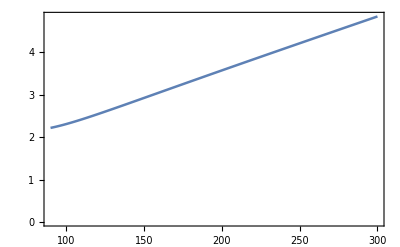

```mathematica
ListPlot[overdiff,Joined->True,BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True]
```

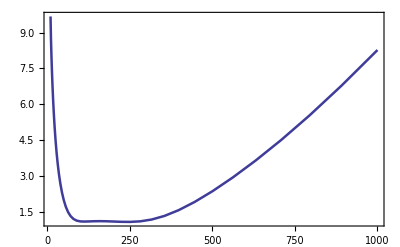

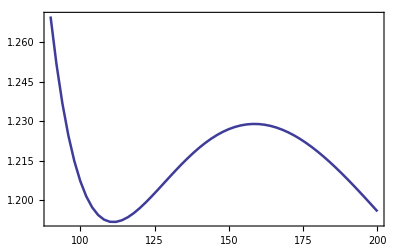

```mathematica
ListPlot[overdiff,Joined->True,BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True]
```

```mathematica
odiff = Map[{#[[1]],Plus @@ (Function[{x},x^2]/@ #[[2]])} &, ss1];
```

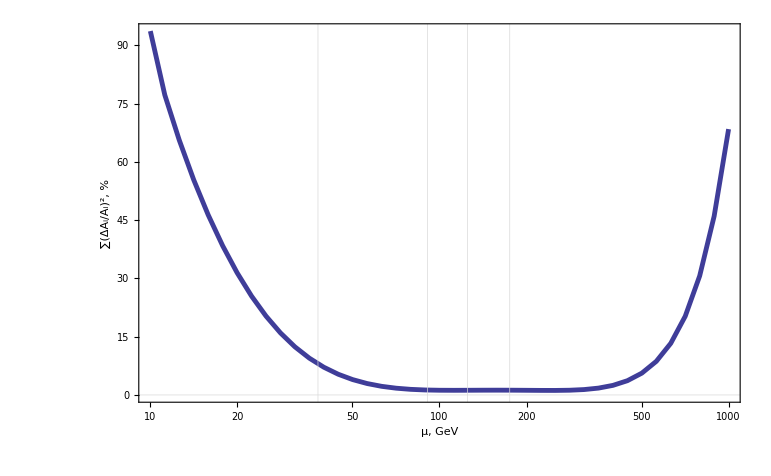

```mathematica
ListLogLinearPlot[ odiff,BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV","∑(ΔA_i/A_i)^2"},GridLines->{{38,91,125,175},{0}},GridLines->{{38,91,125,175},{0}}]
```

```mathematica
names = {"g_1","g_2","g_S","y_t","λ","m","v"}
```

{g_1,g_2,g_S,y_t,λ,m,v}

```mathematica
sslog[[1]]
```

{90,{-0.000788333,0.,0.,-0.0175522,-0.012671,-0.00191513,0.00437284}}

```mathematica
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ ss
```

```mathematica
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ ss1
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ sslog
```

```mathematica
curvesNoAbs[i_]:= Tooltip[{First[#],Identity[ Last[#][[i]]]},names[[i]]] & /@ sslog;
```

```mathematica
curvesNoAbs[i_]:= MapAt[Tooltip[#,names[[i]]] &, ({First[#],Identity[ Last[#][[i]]]} & /@ sslog),{Round[Length[sslog]/10]}];
```

```mathematica
curvesNoAbs[i_]:= MapAt[Tooltip[#,names[[i]]] &, ({First[#],Identity[ Last[#][[i]]]} & /@ ss1),{pos[[i]]}];
```

```mathematica
pos = {2,5,-1,10,10,2,3}
```

{2,5,-1,10,10,2,3}

```mathematica
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ ss1
```

```mathematica
xxx=ListPlot[ Table[curvesNoAbs[i],{i,{1,2,4,5,6,7}}],BaseStyle->20,Background->None(*,PlotStyle->Thickness[0.0045]*),PlotRange->{{50,300},Automatic},PlotMarkers->{Automatic,1},Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV","ΔA/A, %"},GridLines->{{{PDG`MZ,Blue},110,{PDG`MH,Red},240,{PDG`MT,Blue}},{0}}] /. Tooltip[x_,y_]:> Text[y,Sequence @@ Last[x] /. Point->Identity,{-1,0},Background->White]
```

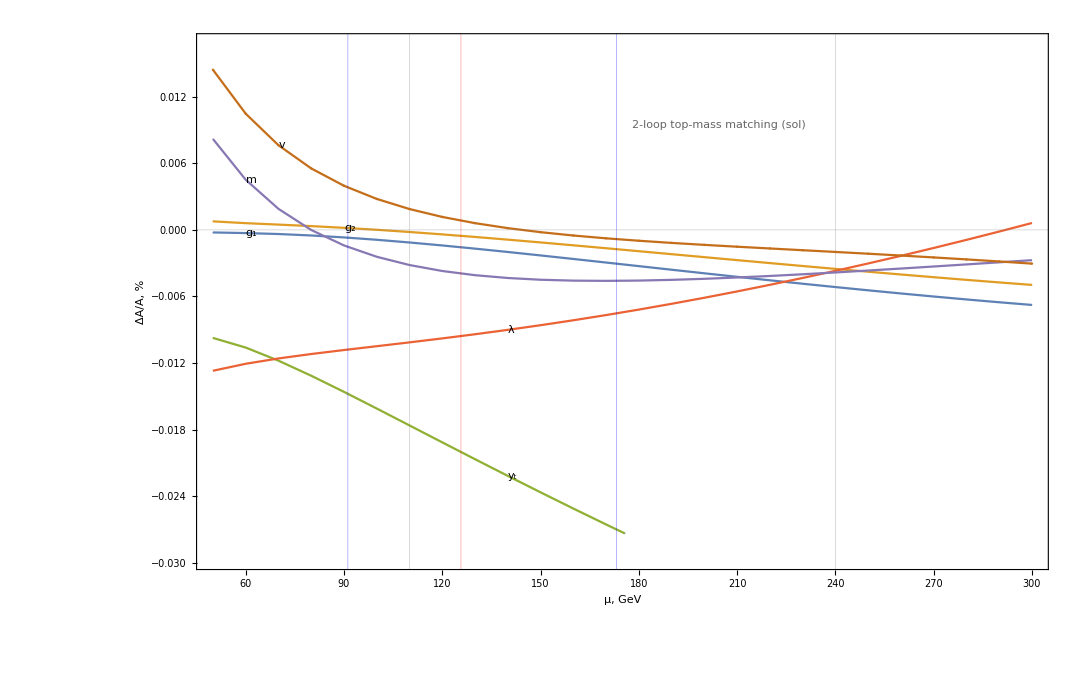

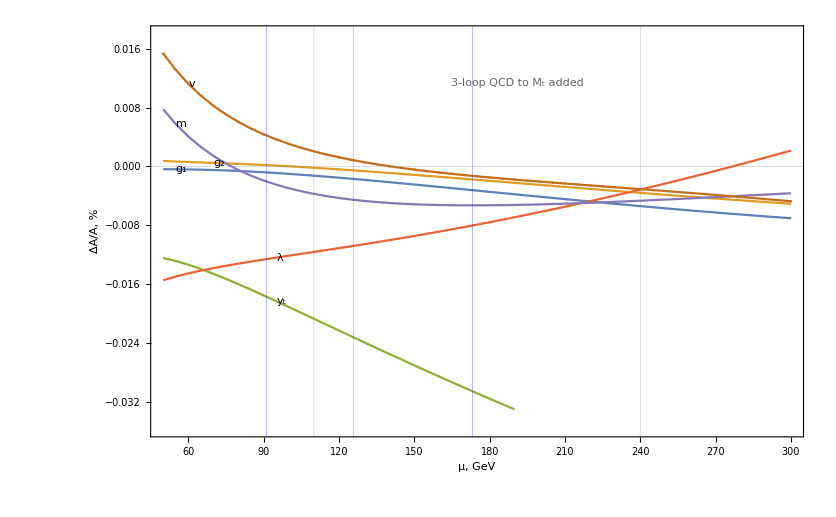

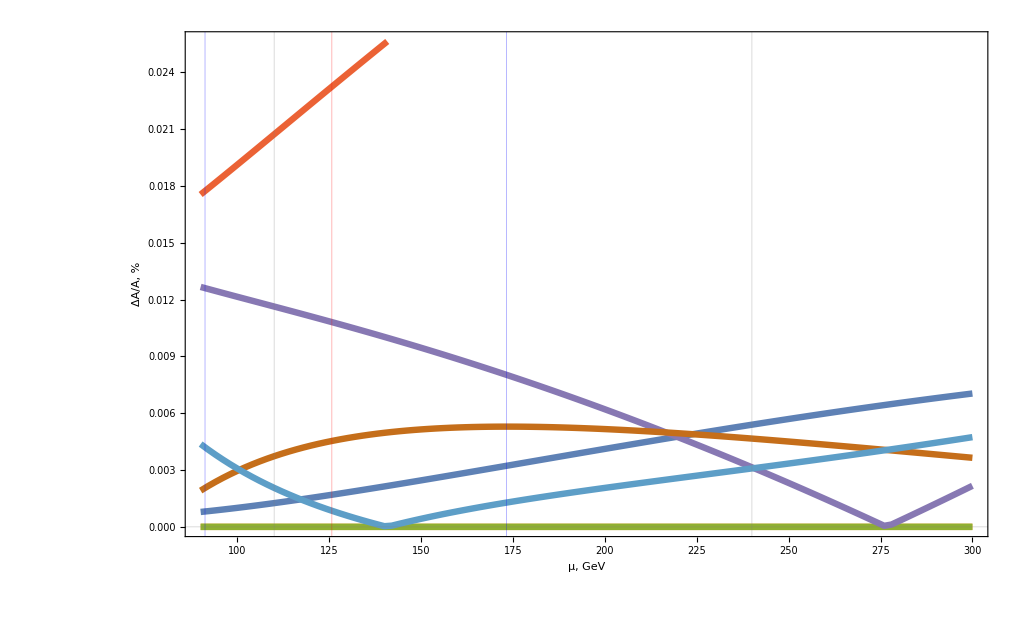

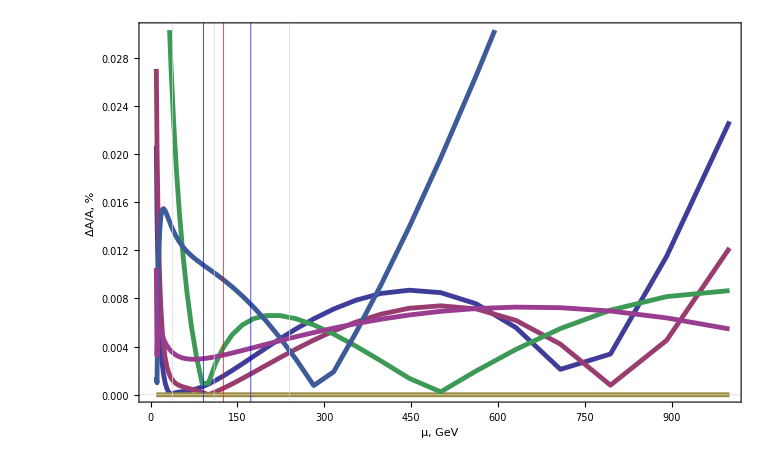

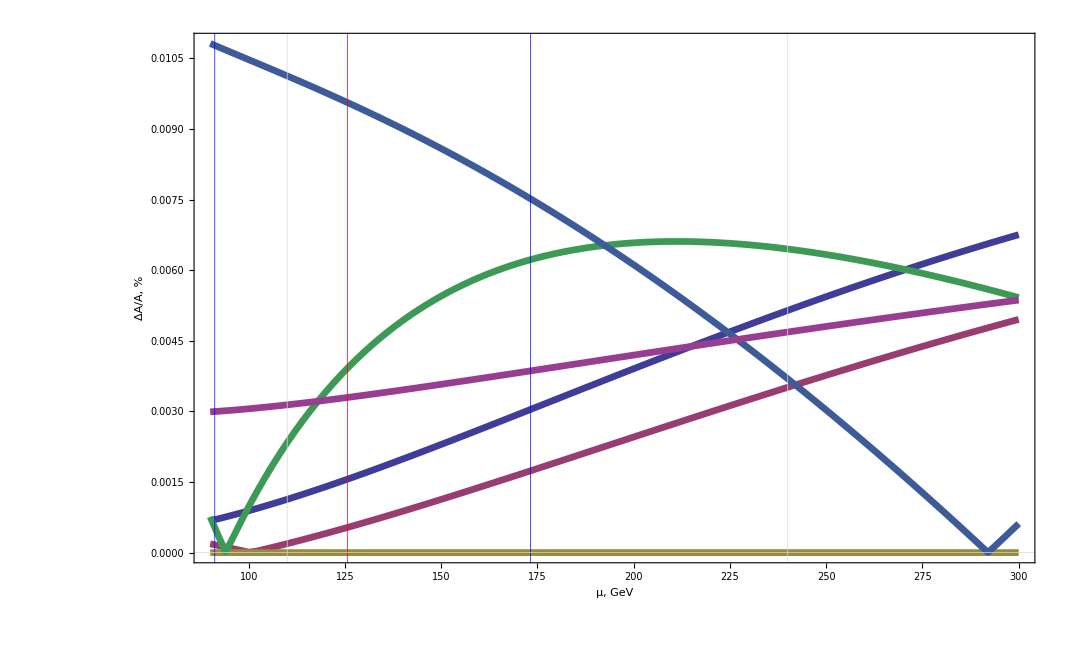

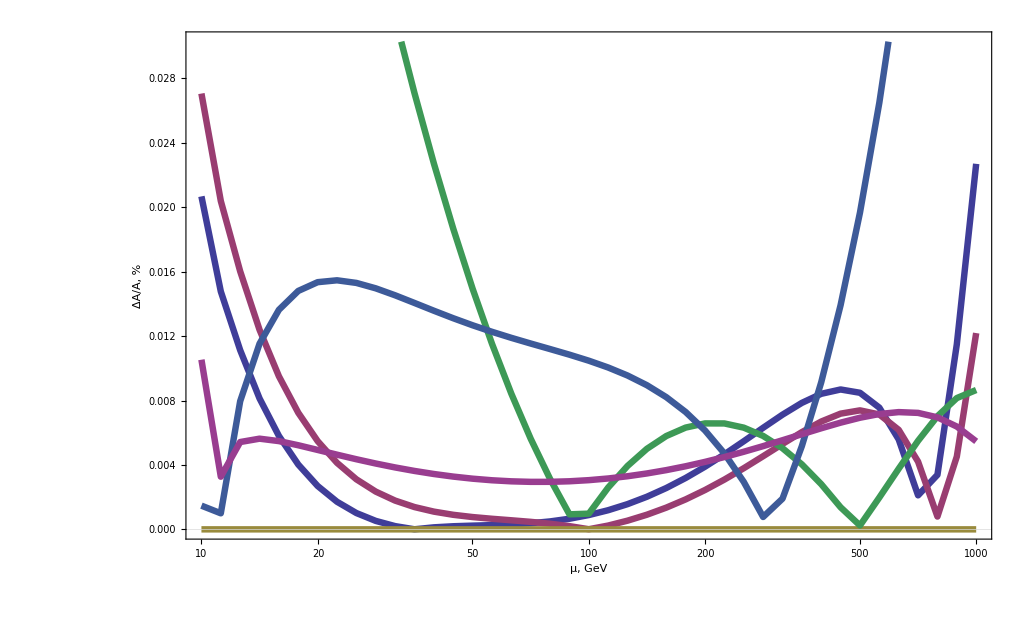

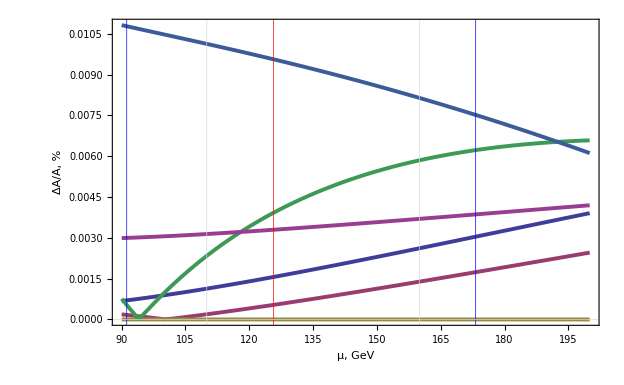

```mathematica
ListPlot[ Evaluate[Table[curves[i],{i,1,7}]],BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV","ΔA/A, %"},GridLines->{{38,{PDG`MZ,Blue},110,{PDG`MH,Red},240,{PDG`MT,Blue}},{0}}]
```

Part::partw: Part TraditionalForm`1 of TraditionalForm`{} does not exist.

Part::partw: Part TraditionalForm`2 of TraditionalForm`{} does not exist.

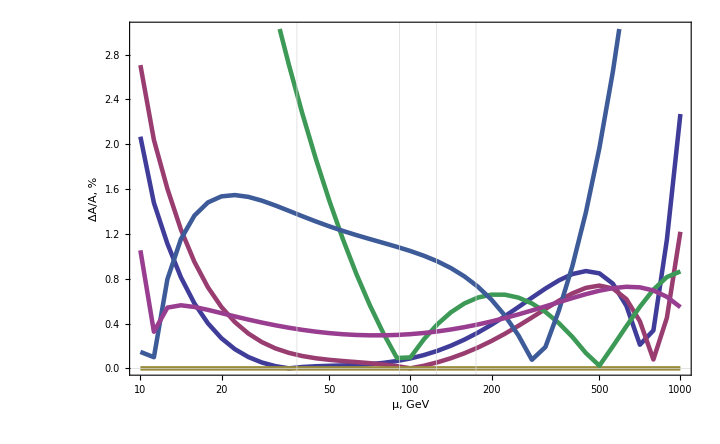

```mathematica
ListLogLinearPlot[ Table[curves[i],{i,1,6}],BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV","ΔA/A, %"},GridLines->{{38,91,125,175},{0}},GridLines->{{38,91,125,175},{0}}]
```

#### Pole masses

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Remove[Global`ND]
```

```mathematica
(*check[obs_,sol_]:= 2Last[Last[sol]]ND[ obs[Sequence @@ ( Most[Last /@ sol]),mu],mu,Last[Last[sol]]]/Symbol["PDG`"  <> ToString[obs]]*)
```

```mathematica
tsolMT=sol2loopMT[PDG`MT][]
```

{g1→0.359473,g2→0.649242,gs→1.16528,yt→0.961655,lam→0.128094,m→132.47,yb→0,scale→173.21}

```mathematica
tsol = RunParsFromPoleMassesAndGfalpha[][PDG`MT]
```

```mathematica
zsol = RunParsFromPoleMassesAndGfalpha[][PDG`MZ]
```

DEBUG: 1/aewSol = 128.204

{g1→0.357007,g2→0.651477,gs→1.214759410656577694,yb→0.46976,yt→0.972163,lam→0.140954,mcheck→130.46,m→130.65,vev→246.069,scale→91.1876}

```mathematica
tsolMta = RunParsFromPoleMassesAndGf[][PDG`MT]
```

{g1→0.358381,g2→0.648116,gs→1.165283670430628306,yb→0.459059,yt→0.936384,lam→0.127139,mcheck→131.96,m→131.864,vev→261.501,scale→173.21}

```mathematica
ExplictScaleDep[obs_,sol_]:= Module[{mu,s0=scale /. sol, pars = {g1,g2,gs,yb,yt,lam,m} /. sol}, s0 ND[ obs[Sequence @@pars ,mu],mu,s0,Scale->0.1]/Symbol["PDG`"  <> ToString[obs]]]
```

```mathematica
check[MT,tsol]
```

-0.121641

```mathematica
ExplictScaleDep[#,tsol] & /@ {MW,MZ,MT,MH,GF}
```

{-0.0940081,-0.0980611,-0.0608205,-0.0190257,0.200994}

{-0.188016,-0.196122,-0.121641,-0.0380514,0.401987}

{-0.211164,-0.219375,-0.144821,-0.0374918,0.438549}

```mathematica
check[#,s91] & /@ {MW,MZ,MT,MH,GF}
```

{-0.202985,-0.211105,-0.11675,-0.0397194,0.435795}

```mathematica
(*numericBeta[iscale_,oscale_:-1]:= Module[{sol=sol[iscale][],ss=oscale},If[ss<0,ss=iscale];ss ND[RunSM[Sequence @@ (Last /@ sol),mu],mu,ss]]*)
```

```mathematica
numericBeta[sol_]:= Module[{mu,ss =scale /. sol, pars = {g1,g2,gs,yb,yt,lam,m} /. sol},ss ND[RunSM[Sequence @@pars,ss,mu],mu,ss]]
```

```mathematica
numericBeta[tsol]
```

{0.00203186,-0.00525701,-0.0723741,-0.0313631,-0.0519094,-0.0197638,2.61358,173.21}

```mathematica
checkExplicitscale[obs_,scale_]:= Module[{sol = sol[scale][]},(*Print[sol];*)Last[Last[sol]]ND[ obs[Sequence @@ ( Most[Last /@ sol]),mu],mu,Last[Last[sol]],Scale->0.1]/Symbol["PDG`"  <> ToString[obs]]]
```

```mathematica
{#,checkscale[MT,#]} &/@ scales
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

{gp→0.357815,g→0.650613,gs→1.19931,yt→0.978123,lam→0.138141,mu0→131.325,mu→110}

{gp→0.358098,g→0.650296,gs→1.19249,yt→0.974556,lam→0.136176,mu0→131.544,mu→120}

{gp→0.358372,g→0.650026,gs→1.18632,yt→0.971452,lam→0.134388,mu0→131.746,mu→130}

{gp→0.358639,g→0.649796,gs→1.1807,yt→0.968726,lam→0.132748,mu0→131.932,mu→140}

{gp→0.358898,g→0.649599,gs→1.17554,yt→0.966314,lam→0.131232,mu0→132.107,mu→150}

{gp→0.35915,g→0.649429,gs→1.17077,yt→0.964167,lam→0.129821,mu0→132.269,mu→160}

{gp→0.359396,g→0.649284,gs→1.16634,yt→0.962243,lam→0.128501,mu0→132.423,mu→170}

{gp→0.359635,g→0.649159,gs→1.16222,yt→0.960512,lam→0.127259,mu0→132.567,mu→180}

{gp→0.359867,g→0.649051,gs→1.15836,yt→0.958948,lam→0.126087,mu0→132.704,mu→190}

{gp→0.360093,g→0.648959,gs→1.15473,yt→0.957529,lam→0.124975,mu0→132.834,mu→200}

{gp→0.360312,g→0.648879,gs→1.15131,yt→0.956236,lam→0.123918,mu0→132.958,mu→210}

{gp→0.360524,g→0.648809,gs→1.14808,yt→0.955056,lam→0.122909,mu0→133.076,mu→220}

{gp→0.36073,g→0.648749,gs→1.14502,yt→0.953976,lam→0.121944,mu0→133.189,mu→230}

{gp→0.36093,g→0.648696,gs→1.14211,yt→0.952984,lam→0.121018,mu0→133.297,mu→240}

{gp→0.361122,g→0.64865,gs→1.13934,yt→0.952072,lam→0.120128,mu0→133.4,mu→250}

{gp→0.361309,g→0.648608,gs→1.1367,yt→0.951231,lam→0.119271,mu0→133.5,mu→260}

{gp→0.361489,g→0.648571,gs→1.13418,yt→0.950454,lam→0.118443,mu0→133.595,mu→270}

{gp→0.361662,g→0.648537,gs→1.13176,yt→0.949736,lam→0.117643,mu0→133.688,mu→280}

{gp→0.361829,g→0.648506,gs→1.12945,yt→0.94907,lam→0.116868,mu0→133.777,mu→290}

{gp→0.361989,g→0.648476,gs→1.12722,yt→0.948452,lam→0.116117,mu0→133.862,mu→300}

(100 | -0.120675
110 | -0.124764
120 | -0.12853
130 | -0.132025
140 | -0.135288
150 | -0.138352
160 | -0.14124
170 | -0.143974
180 | -0.14657
190 | -0.149042
200 | -0.151401
210 | -0.153658
220 | -0.155822
230 | -0.157899
240 | -0.159896
250 | -0.161818
260 | -0.163671
270 | -0.165458
280 | -0.167183
290 | -0.16885
300 | -0.170462)

```mathematica
ListPlot[{#,checkscale[MT,#]} &/@ scales,Joined->True]
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

{gp→0.357815,g→0.650613,gs→1.19931,yt→0.978123,lam→0.138141,mu0→131.325,mu→110}

{gp→0.358098,g→0.650296,gs→1.19249,yt→0.974556,lam→0.136176,mu0→131.544,mu→120}

{gp→0.358372,g→0.650026,gs→1.18632,yt→0.971452,lam→0.134388,mu0→131.746,mu→130}

{gp→0.358639,g→0.649796,gs→1.1807,yt→0.968726,lam→0.132748,mu0→131.932,mu→140}

{gp→0.358898,g→0.649599,gs→1.17554,yt→0.966314,lam→0.131232,mu0→132.107,mu→150}

{gp→0.35915,g→0.649429,gs→1.17077,yt→0.964167,lam→0.129821,mu0→132.269,mu→160}

{gp→0.359396,g→0.649284,gs→1.16634,yt→0.962243,lam→0.128501,mu0→132.423,mu→170}

{gp→0.359635,g→0.649159,gs→1.16222,yt→0.960512,lam→0.127259,mu0→132.567,mu→180}

{gp→0.359867,g→0.649051,gs→1.15836,yt→0.958948,lam→0.126087,mu0→132.704,mu→190}

{gp→0.360093,g→0.648959,gs→1.15473,yt→0.957529,lam→0.124975,mu0→132.834,mu→200}

{gp→0.360312,g→0.648879,gs→1.15131,yt→0.956236,lam→0.123918,mu0→132.958,mu→210}

{gp→0.360524,g→0.648809,gs→1.14808,yt→0.955056,lam→0.122909,mu0→133.076,mu→220}

{gp→0.36073,g→0.648749,gs→1.14502,yt→0.953976,lam→0.121944,mu0→133.189,mu→230}

{gp→0.36093,g→0.648696,gs→1.14211,yt→0.952984,lam→0.121018,mu0→133.297,mu→240}

{gp→0.361122,g→0.64865,gs→1.13934,yt→0.952072,lam→0.120128,mu0→133.4,mu→250}

{gp→0.361309,g→0.648608,gs→1.1367,yt→0.951231,lam→0.119271,mu0→133.5,mu→260}

{gp→0.361489,g→0.648571,gs→1.13418,yt→0.950454,lam→0.118443,mu0→133.595,mu→270}

{gp→0.361662,g→0.648537,gs→1.13176,yt→0.949736,lam→0.117643,mu0→133.688,mu→280}

{gp→0.361829,g→0.648506,gs→1.12945,yt→0.94907,lam→0.116868,mu0→133.777,mu→290}

{gp→0.361989,g→0.648476,gs→1.12722,yt→0.948452,lam→0.116117,mu0→133.862,mu→300}

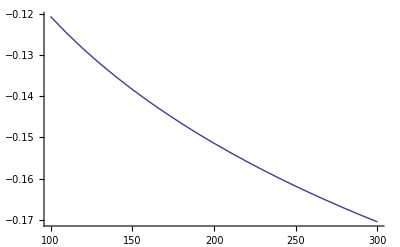

```mathematica
ListPlot[{#,checkscale[MT,#]} &/@ scales,Joined->True]
```

```mathematica
ListPlot[{#,checkscale[MZ,#]} &/@ scales,Joined->True]
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

{gp→0.357815,g→0.650613,gs→1.19931,yt→0.978123,lam→0.138141,mu0→131.325,mu→110}

{gp→0.358098,g→0.650296,gs→1.19249,yt→0.974556,lam→0.136176,mu0→131.544,mu→120}

{gp→0.358372,g→0.650026,gs→1.18632,yt→0.971452,lam→0.134388,mu0→131.746,mu→130}

{gp→0.358639,g→0.649796,gs→1.1807,yt→0.968726,lam→0.132748,mu0→131.932,mu→140}

{gp→0.358898,g→0.649599,gs→1.17554,yt→0.966314,lam→0.131232,mu0→132.107,mu→150}

{gp→0.35915,g→0.649429,gs→1.17077,yt→0.964167,lam→0.129821,mu0→132.269,mu→160}

{gp→0.359396,g→0.649284,gs→1.16634,yt→0.962243,lam→0.128501,mu0→132.423,mu→170}

{gp→0.359635,g→0.649159,gs→1.16222,yt→0.960512,lam→0.127259,mu0→132.567,mu→180}

{gp→0.359867,g→0.649051,gs→1.15836,yt→0.958948,lam→0.126087,mu0→132.704,mu→190}

{gp→0.360093,g→0.648959,gs→1.15473,yt→0.957529,lam→0.124975,mu0→132.834,mu→200}

{gp→0.360312,g→0.648879,gs→1.15131,yt→0.956236,lam→0.123918,mu0→132.958,mu→210}

{gp→0.360524,g→0.648809,gs→1.14808,yt→0.955056,lam→0.122909,mu0→133.076,mu→220}

{gp→0.36073,g→0.648749,gs→1.14502,yt→0.953976,lam→0.121944,mu0→133.189,mu→230}

{gp→0.36093,g→0.648696,gs→1.14211,yt→0.952984,lam→0.121018,mu0→133.297,mu→240}

{gp→0.361122,g→0.64865,gs→1.13934,yt→0.952072,lam→0.120128,mu0→133.4,mu→250}

{gp→0.361309,g→0.648608,gs→1.1367,yt→0.951231,lam→0.119271,mu0→133.5,mu→260}

{gp→0.361489,g→0.648571,gs→1.13418,yt→0.950454,lam→0.118443,mu0→133.595,mu→270}

{gp→0.361662,g→0.648537,gs→1.13176,yt→0.949736,lam→0.117643,mu0→133.688,mu→280}

{gp→0.361829,g→0.648506,gs→1.12945,yt→0.94907,lam→0.116868,mu0→133.777,mu→290}

{gp→0.361989,g→0.648476,gs→1.12722,yt→0.948452,lam→0.116117,mu0→133.862,mu→300}

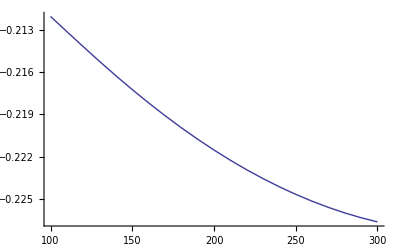

```mathematica
RunSM[Sequence @@ (Last /@ s91), PDG`MT]
```

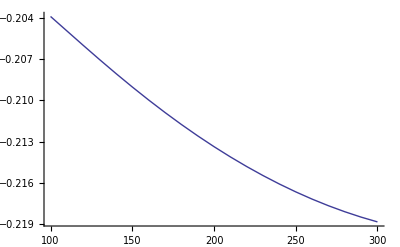

```mathematica
ListPlot[{#,checkscale[MW,#]} &/@ scales,Joined->True]
```

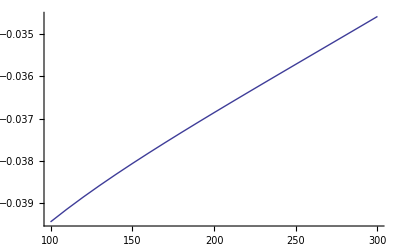

```mathematica
ListPlot[{#,checkscale[MH,#]} &/@ scales,Joined->True]
```

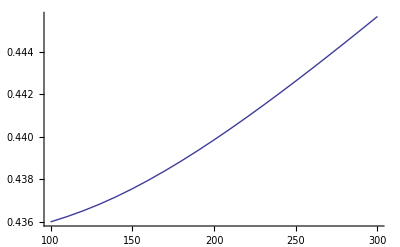

```mathematica
ListPlot[{#,checkscale[GF,#]} &/@ scales,Joined->True]
```

```mathematica
rr = RunSM[Sequence @@ (Last /@ s91), PDG`MT]
```

{0.358557661771828428,0.6479785593759323419,1.165002622973601411,0.9497487829378230192,0.127719318006899446,132.2994282778492337,173.210000000000008}

```mathematica
PDG`MT  ND[RunSM[Sequence @@ (Last /@ s91), mu],mu,PDG`MT]
```

{0.00203502,-0.00525068,-0.072294,-0.0538173,-0.0215114,2.14155,173.21}

```mathematica
nr = (Last /@ s172)
```

{0.359473,0.649242,1.16499,0.961668,0.128094,132.47,173.21}

```mathematica
100(1-nr/rr)
```

{-0.255378,-0.194954,0.00125722,-1.25499,-0.293387,-0.128929,0.}

```mathematica
smt10 = sol[10 PDG`MT][];
```

```mathematica
smtd10 = sol[PDG`MT/10][];
```

```mathematica
numericBeta[PDG`MZ,PDG`MT]
```

{0.00203502,-0.00525068,-0.072294,-0.0538173,-0.0215114,2.14155,173.21}

```mathematica
numericBeta[PDG`MZ,PDG`MZ]
```

{0.00201616,-0.00531678,-0.0821164,-0.0610575,-0.0246032,2.37762,91.1876}

```mathematica
Clear[NumGrad]
```

```mathematica
(*NumGrad[obs_,scale_,s_:0.1]:= Module[{sl = sol[scale][],pars,tpars},pars = Most[ Last /@ sl];tpars =Table[{ReplacePart[pars,i->xxxx],pars[[i]]},{i,Length[pars]}]; Map[ND[obs[Sequence @@ First[#], scale],xxxx,Last[#],Scale->s] &,tpars]]*)
```

```mathematica
NumGrad[obs_,sol_,s_:0.1]:= Module[{xxxx,ss = scale /.sol,pars = {g1,g2,gs,yb,yt,lam,m,scale} /. sol,tpars},tpars =Table[{ReplacePart[Most[pars],i->xxxx],pars[[i]]},{i,Length[pars]-1}]; (*Print[tpars];*)Map[ND[obs[Sequence @@ First[#], ss],xxxx,Last[#],Scale->s] &,tpars]]
```

```mathematica
NumGrad[MT,tsol]/PDG`MT //TableForm
```

0.00750579
0.0216548
0.0162895
0.
0.830137
-3.57797
0.00785068

0.372968
1.87366
0.688143
-27.4032
51.5371
0.979708

```mathematica
NumGrad1[obs_,scale_]:= Module[{sl = sol[scale][],pars,tpars},pars = Most[ Last /@ sl];tpars =Table[{ReplacePart[pars,i->xxxx],pars[[i]]},{i,Length[pars]}]; Map[ND[obs[Sequence @@ First[#], scale],xxxx,Last[#],Scale->0.1] &,tpars]]
```

```mathematica
(*checkImplicitScale[obs_,scale]:= Module[{sol = sol[scale][]},(*Print[sol];*)Most[numericBeta[scale]]. NumGrad[obs,scale]/Symbol["PDG`"  <> ToString[obs]]]*)
checkImplicitScale[obs_,sol_]:= Module[{ss = scale /. sol},(*Print[sol];*)Most[numericBeta[sol]]. NumGrad[obs,sol]/Symbol["PDG`"  <> ToString[obs]]]
```

```mathematica
checkImplicitScale[MZ,sol[PDG`MZ][]]+x ExplictScaleDep[MZ,sol[PDG`MZ][]]
```

0.106238-0.106924 x

```mathematica
mzsol=sol[PDG`MZ][]
```

{g1→0.357297,g2→0.651358,gs→1.21476,yt→0.989407,lam→0.142731,m→130.919,yb→0,scale→91.1876}

```mathematica
checkImplicitScale[MT,tsolMT]+x ExplictScaleDep[MT,tsolMT]
```

0.0556109-0.0744619 x

```mathematica
checkImplicitScale[MZ,tsol]+x ExplictScaleDep[MZ,tsol]
```

0.101878-0.0980611 x

```mathematica
checkImplicitScale[MZ,PDG`MZ]+x checkExplicitscale[MZ,PDG`MZ]
```

0.104869-0.105553 x

-0.000683953

```mathematica
(checkImplicitScale[#,mtsol]+x ExplictScaleDep[#,mtsol]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.107773-0.107304 x
0.111888-0.111416 x
0.057609-0.0765028 x
0.0207684-0.01868 x
-0.232827+0.222485 x

```mathematica
% /. x->1
```

{0.000468756,0.00047187,-0.0188938,0.00208835,-0.0103416}

```mathematica
(checkImplicitScale[#,tsol]+x ExplictScaleDep[#,tsol]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.097843-0.0940081 x
0.101878-0.0980611 x
0.0468631-0.0608205 x
0.0247942-0.0190257 x
-0.216031+0.200994 x

```mathematica
% /. x->1
```

{0.00383489,0.00381645,-0.0139574,0.00576849,-0.0150375}

```mathematica
(checkImplicitScale[#,zsol]+x ExplictScaleDep[#,zsol]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.0977303-0.0953613 x
0.101762-0.0993949 x
0.0443336-0.0524957 x
0.0254246-0.0198633 x
-0.216819+0.209074 x

```mathematica
%  /. x->1
```

{0.00236903,0.00236747,-0.00816204,0.00556131,-0.00774525}

```mathematica
(checkImplicitScale[#,mzsol]+x ExplictScaleDep[#,mzsol]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.102166-0.102858 x
0.106238-0.106924 x
0.0484621-0.0615327 x
0.0212354-0.0198556 x
-0.222622+0.220626 x

```mathematica
%16 /. x->1
```

{-0.000692072,-0.000685904,-0.0130706,0.0013798,-0.00199659}

```mathematica
LogMuDerivative[obs_,scale_]:= Module[{ss = RunParsFromPoleMassesAndGf[][scale]},(checkImplicitScale[obs,ss]+ ExplictScaleDep[obs,ss])]
```

```mathematica
mtlogmu = {#, LogMuDerivative[MT,#] }& /@ scales;
```

ReplaceAll::reps: {50, 60, 70, 80, 90, 100, 110, 120, 130, 140, 150, 160, 170, 180, 190, 200, 210, 220, 230, 240, 250, 260, 270, 280, 290, 300} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
mhlogmu = {#, LogMuDerivative[MH,#] }& /@ scales;
```

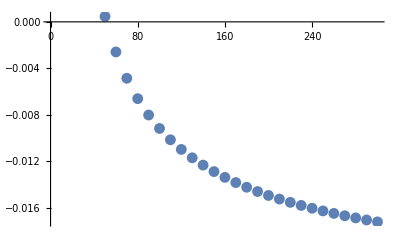

```mathematica
ListPlot[mtlogmu]
```

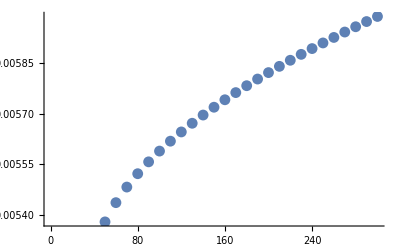

```mathematica
ListPlot[mhlogmu]
```

```mathematica
scale
```

```mathematica
sol
```

```mathematica
mtsol=sol[PDG`MT][]
```

{g1→0.359538,g2→0.64926,gs→1.16528,yt→0.965045,lam→0.128159,m→132.563,yb→0,scale→173.21}

```mathematica
Collect[MTp[Sequence @@ ({g1,g2,gs,yb,yt,lam,m,scale} /. tsol),3] /. as->h as /. aew->h aew,h,Expand]
```

173.147+(-8.871513202915086427 aew+7.944998922998824428 as) h+(-0.1455403931607879445 aew^2-0.8612677090012975746 aew as-1.86994124956751253 as^2) h^2-0.5666402091457769147 as^3 h^3

```mathematica
MTp[Sequence @@ ({g1,g2,gs,yb,yt,lam,m,scale} /. tsol),3] /. as->h /. aew->h /. h->1//Expand
```

168.777

```mathematica
Collect[MTp[Sequence @@ ({g1,g2,gs,yb,yt,lam,m,scale} /. zsol),3] /. as->h as /. aew->h aew,h,Expand]
```

169.154+(3.17100098919087668 aew+0.6168188708907472263 as) h+(0.0792289637458516626 aew^2-0.8838164417897662841 aew as-1.014244735289162389 as^2) h^2-0.4906404730349674063 as^3 h^3

```mathematica
MTp[Sequence @@ ({g1,g2,gs,yb,yt,lam,m,scale} /. zsol),3]/. as->h /. aew->h /. h->1//Expand
```

170.632

```mathematica
PDG`MT
```

173.21

```mathematica
% /. x->1
```

{-0.000692072,-0.000685904,-0.0130706,0.0013798,-0.00199659}

```mathematica
(checkImplicitScale[#,PDG`MZ]+x checkExplicitscale[#,PDG`MZ]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.100803-0.101493 x
0.104869-0.105553 x
0.0457875-0.0583751 x
0.0212328-0.0198597 x
0.217897 x-0.219877

```mathematica
(checkImplicitScale[#,PDG`MZ]+x checkExplicitscale[#,PDG`MZ]) &/@ {MW,MZ,MT,MH,GF}  /. x->1//TableForm
```

-0.000690165
-0.000683953
-0.0125876
0.0013731
-0.00197953

```mathematica
(checkImplicitScale[#,PDG`MT]+x checkExplicitscale[#,PDG`MT]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.106112-0.105582 x
0.110218-0.109687 x
0.0544809-0.0724107 x
0.0207942-0.0187459 x
0.219274 x-0.229489

```mathematica
(checkImplicitScale[#,PDG`MT]+x checkExplicitscale[#,PDG`MT]) &/@ {MW,MZ,MT,MH,GF} /. x->1//TableForm
```

0.000529465
0.000530784
-0.0179298
0.00204835
-0.0102145

0.000529465
0.000530784
-0.0179298
0.00204835
-0.0102145

```mathematica
LogMuDerivative[obs_,scale_]:= 100*(checkImplicitScale[obs,scale]+ checkExplicitscale[obs,scale]); (* d Log/ d Log[mu], in percents *)
```

```mathematica
LogMuDerivative[MT,PDG`MZ]
```

-1.25876

0.000529465

```mathematica
MWscaledep ={#, LogMuDerivative[MW,#]} & /@ scales;
MZscaledep ={#,  LogMuDerivative[MZ,#]} & /@ scales;
MTscaledep = {#, LogMuDerivative[MT,#] }& /@ scales;
MHscaledep ={#,  LogMuDerivative[MH,#]} & /@ scales;
GFscaledep = {#, LogMuDerivative[GF,#]} & /@ scales;
```

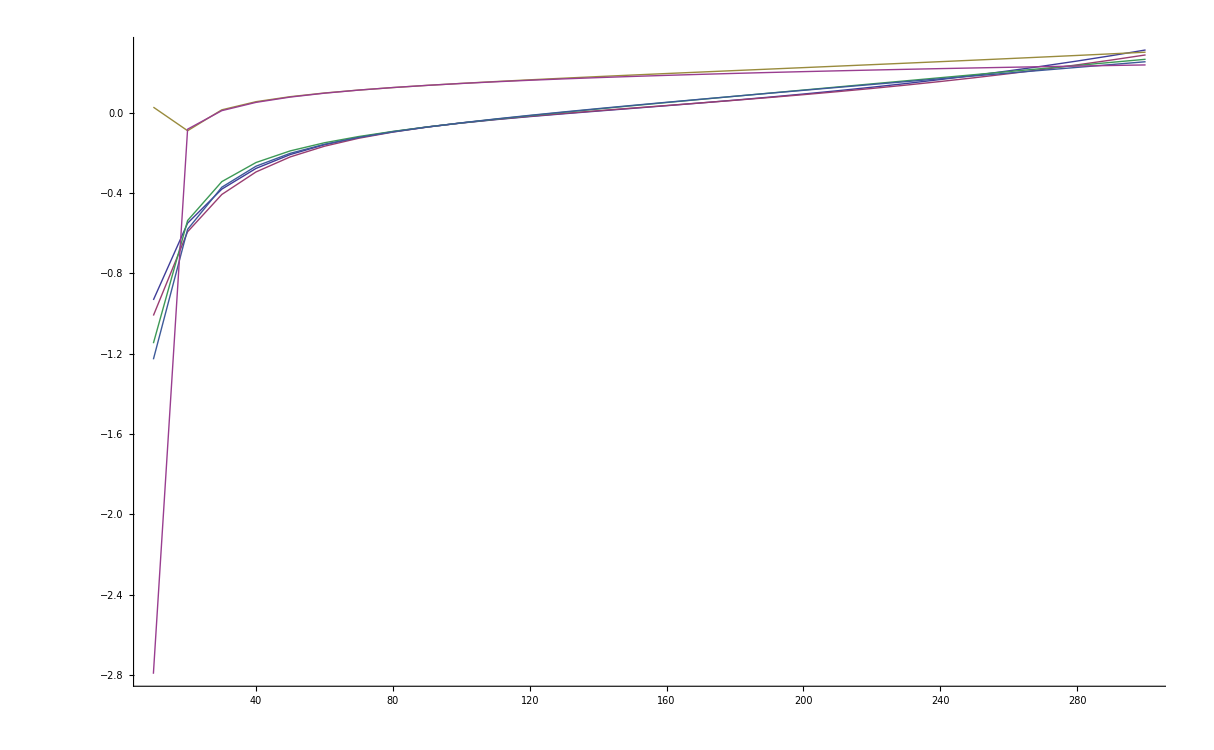

```mathematica
ListPlot[{MZscaledep,MWscaledep,MHscaledep,mZscaledep,mWscaledep,mHscaledep},Joined->True]
```

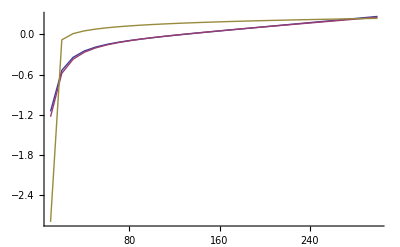

```mathematica
ListPlot[{mZscaledep,mWscaledep,mHscaledep},Joined->True]
```

```mathematica
xxx=Tooltip[GFscaledep,"G_F"];
```

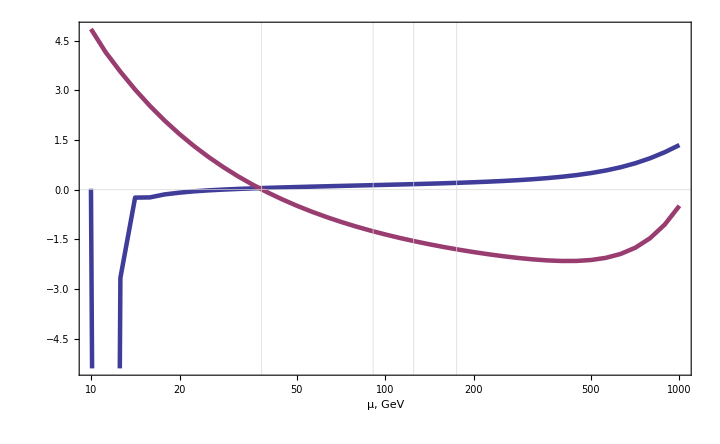

```mathematica
ListLogLinearPlot[{Tooltip[MHscaledep,"M_H"],Tooltip[MTscaledep,"M_t"]},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV",""},GridLines->{{38,91,125,175},{0}},ImageSize->{72 10,72 7}]
```

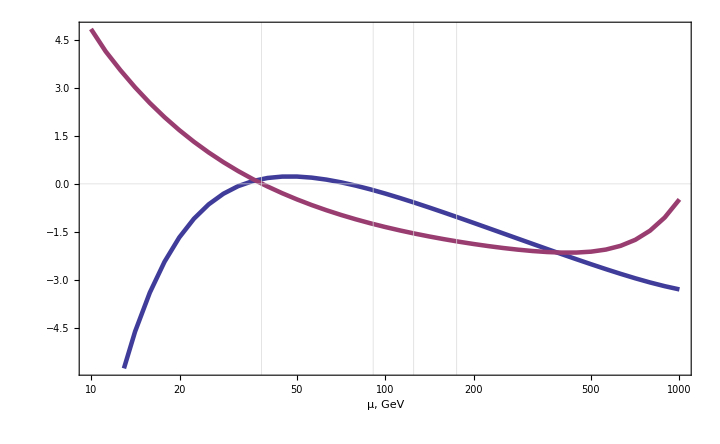

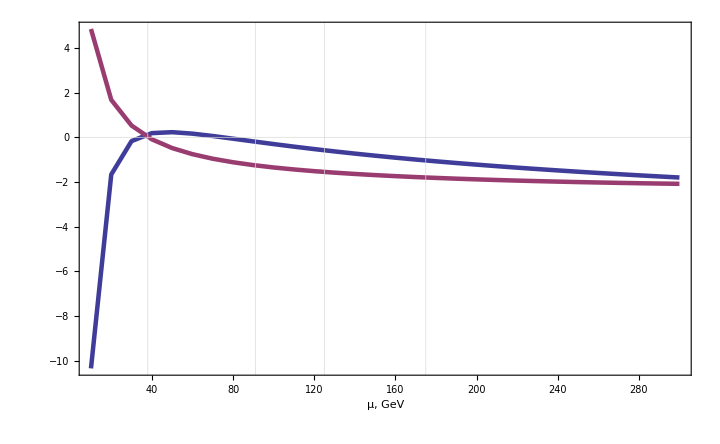

```mathematica
ListLogLinearPlot[{Tooltip[GFscaledep,"G_F"],Tooltip[MTscaledep,"M_t"]},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV",""},GridLines->{{38,91,125,175},{0}},ImageSize->{72 10,72 7}]
```

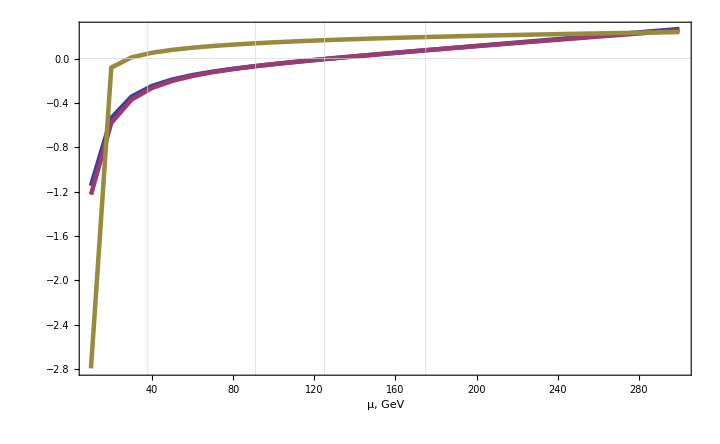

```mathematica
ListPlot[{mZscaledep,mWscaledep,mHscaledep},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV",""},GridLines->{{38,91,125,175},{0}},ImageSize->{72 10,72 7}]
```

```mathematica
xxx //FullForm
```

Tooltip[List[List[10,-10.3482],List[20,-1.66533],List[30,-0.169803],List[40,0.187077],List[50,0.229603],List[60,0.163801],List[70,0.0579141],List[80,-0.0616098],List[90,-0.183574],List[100,-0.303058],List[110,-0.417939],List[120,-0.527412],List[130,-0.631304],List[140,-0.72975],List[150,-0.823024],List[160,-0.911458],List[170,-0.995398],List[180,-1.07518],List[190,-1.15112],List[200,-1.22351],List[210,-1.29263],List[220,-1.35871],List[230,-1.42199],List[240,-1.48265],List[250,-1.54089],List[260,-1.59686],List[270,-1.65072],List[280,-1.70261],List[290,-1.75265],List[300,-1.80095]],"G_F"]

```mathematica
ListPlot[{Tooltip[GFscaledep,"G_F"],Tooltip[MTscaledep,"M_t"],gFscaledep,mTscaledep},Joined->True]//FullForm
```

Graphics[List[Hue[0.67,0.6,0.6],Line[List[List[10.,-10.3482],List[20.,-1.66533],List[30.,-0.169803],List[40.,0.187077],List[50.,0.229603],List[60.,0.163801],List[70.,0.0579141],List[80.,-0.0616098],List[90.,-0.183574],List[100.,-0.303058],List[110.,-0.417939],List[120.,-0.527412],List[130.,-0.631304],List[140.,-0.72975],List[150.,-0.823024],List[160.,-0.911458],List[170.,-0.995398],List[180.,-1.07518],List[190.,-1.15112],List[200.,-1.22351],List[210.,-1.29263],List[220.,-1.35871],List[230.,-1.42199],List[240.,-1.48265],List[250.,-1.54089],List[260.,-1.59686],List[270.,-1.65072],List[280.,-1.70261],List[290.,-1.75265],List[300.,-1.80095]]],Hue[0.906068,0.6,0.6],Line[List[List[10.,4.85033],List[20.,1.67662],List[30.,0.526149],List[40.,-0.0905856],List[50.,-0.481825],List[60.,-0.755261],List[70.,-0.958881],List[80.,-1.11747],List[90.,-1.24519],List[100.,-1.35074],List[110.,-1.43977],List[120.,-1.51612],List[130.,-1.58248],List[140.,-1.64081],List[150.,-1.69256],List[160.,-1.73884],List[170.,-1.78048],List[180.,-1.81816],List[190.,-1.8524],List[200.,-1.88364],List[210.,-1.91221],List[220.,-1.9384],List[230.,-1.96243],List[240.,-1.98452],List[250.,-2.00481],List[260.,-2.02345],List[270.,-2.04054],List[280.,-2.0562],List[290.,-2.07049],List[300.,-2.0835]]],Hue[0.142136,0.6,0.6],Line[List[List[10.,-10.4684],List[20.,-1.66176],List[30.,-0.148625],List[40.,0.206153],List[50.,0.242085],List[60.,0.170147],List[70.,0.060019],List[80.,-0.0616066],List[90.,-0.183682],List[100.,-0.301544],List[110.,-0.41334],List[120.,-0.518507],List[130.,-0.617082],List[140.,-0.709376],List[150.,-0.79581],List[160.,-0.87684],List[170.,-0.952912],List[180.,-1.02445],List[190.,-1.09184],List[200.,-1.15543],List[210.,-1.21555],List[220.,-1.27249],List[230.,-1.3265],List[240.,-1.37781],List[250.,-1.42664],List[260.,-1.47317],List[270.,-1.51757],List[280.,-1.56],List[290.,-1.60059],List[300.,-1.63947]]],Hue[0.378204,0.6,0.6],Line[List[List[10.,4.75517],List[20.,1.67238],List[30.,0.531523],List[40.,-0.0844164],List[50.,-0.47712],List[60.,-0.752368],List[70.,-0.95749],List[80.,-1.11706],List[90.,-1.24518],List[100.,-1.3506],List[110.,-1.43903],List[120.,-1.51436],List[130.,-1.57938],List[140.,-1.63611],List[150.,-1.68606],List[160.,-1.73038],List[170.,-1.76999],List[180.,-1.8056],List[190.,-1.83778],List[200.,-1.867],List[210.,-1.89364],List[220.,-1.91802],List[230.,-1.94041],List[240.,-1.96103],List[250.,-1.98008],List[260.,-1.99771],List[270.,-2.01407],List[280.,-2.02929],List[290.,-2.04346],List[300.,-2.0567]]]],List[Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,True],Rule[PlotRange,Automatic],Rule[PlotRangeClipping,True]]]

```mathematica
ListPlot[{Tooltip[GFscaledep,"G_F"],Tooltip[MTscaledep,"M_t"],gFscaledep,mTscaledep},Joined->True]/.Tooltip[{color___,line_},tip_]:>{color,line,Text[tip,line[[1,-100]],BaseStyle->20,Background->White]}
```

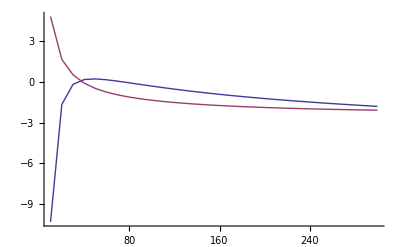

```mathematica
ListPlot[{GFscaledep,MTscaledep},Joined->True]
```

```mathematica
MZscaledep
```

(10 | -0.932013
20 | -0.549905
30 | -0.380423
40 | -0.277277
50 | -0.208339
60 | -0.159261
70 | -0.122578
80 | -0.093998
90 | -0.0708682
100 | -0.051454
110 | -0.0345683
120 | -0.0193673
130 | -0.00523155
140 | 0.00830686
150 | 0.0216104
160 | 0.0349662
170 | 0.0486069
180 | 0.0627245
190 | 0.0774803
200 | 0.0930125
210 | 0.109441
220 | 0.126872
230 | 0.145401
240 | 0.165112
250 | 0.186087
260 | 0.208396
270 | 0.232111
280 | 0.257294
290 | 0.284008
300 | 0.312313)

```mathematica
LogMuDerivativeWithRunning[iscale_][obs_,scale_]:= Module[{sl = sol[iscale][],dummy},dummy[x_?NumericQ]:= Module[{ppp=RunSM[Sequence @@ (Last /@ sl),x]},obs[ Sequence @@ ppp]];
scale/Symbol["PDG`"  <> ToString[obs]] *ND[dummy[xxx],xxx,scale,Scale->0.1]]
```

```mathematica
mttestdep = {#,100*LogMuDerivativeWithRunning[PDG`MZ][MT,#]} &/@ scales;
```

(100 | -1.3506
110 | -1.43903
120 | -1.51436
130 | -1.57938
140 | -1.63611
150 | -1.68606
160 | -1.73038
170 | -1.76999
180 | -1.8056
190 | -1.83778
200 | -1.867
210 | -1.89364
220 | -1.91802
230 | -1.94041
240 | -1.96103
250 | -1.98008
260 | -1.99771
270 | -2.01407
280 | -2.02929
290 | -2.04346
300 | -2.0567)

```mathematica
mttest1dep = {#,100*LogMuDerivativeWithRunning[PDG`MT][MT,#]} &/@ scales;
```

```mathematica
mttest2dep = {#,100*LogMuDerivativeWithRunning[300][MT,#]} &/@ scales;
```

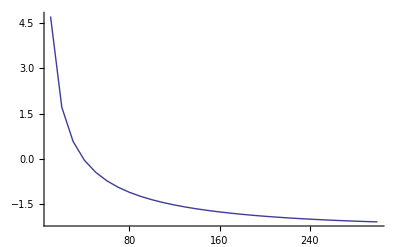

```mathematica
ListPlot[mttest2dep,Joined->True]
```

```mathematica
N
```

```mathematica
MTscaledep
```

(100 | -1.35074
110 | -1.43977
120 | -1.51612
130 | -1.58248
140 | -1.64081
150 | -1.69256
160 | -1.73884
170 | -1.78048
180 | -1.81816
190 | -1.8524
200 | -1.88364
210 | -1.91221
220 | -1.9384
230 | -1.96243
240 | -1.98452
250 | -2.00481
260 | -2.02345
270 | -2.04054
280 | -2.0562
290 | -2.07049
300 | -2.0835)

```mathematica
MTscaledep-mttestdep
```

(0 | -0.000142824
0 | -0.000748648
0 | -0.00175807
0 | -0.0030994
0 | -0.00470418
0 | -0.00650867
0 | -0.00845417
0 | -0.010487
0 | -0.0125578
0 | -0.0146217
0 | -0.016637
0 | -0.0185654
0 | -0.0203714
0 | -0.0220217
0 | -0.0234853
0 | -0.0247329
0 | -0.0257366
0 | -0.0264703
0 | -0.0269086
0 | -0.0270276
0 | -0.0268038)

```mathematica
mWscaledep ={#, 100 LogMuDerivativeWithRunning[PDG`MZ][MW,#]} & /@ scales;
mZscaledep ={#, 100  LogMuDerivativeWithRunning[PDG`MZ][MZ,#]} & /@ scales;
mTscaledep = {#, 100 LogMuDerivativeWithRunning[PDG`MZ][MT,#] }& /@ scales;
mHscaledep ={#,  100 LogMuDerivativeWithRunning[PDG`MZ][MH,#]} & /@ scales;
gFscaledep = {#, 100 LogMuDerivativeWithRunning[PDG`MZ][GF,#]} & /@ scales;
```

```mathematica
ScaleDep[iscale_][obs_,scale_]:= Module[{sl = sol[iscale][],dummy},dummy[x_?NumericQ]:= Module[{ppp=RunSM[Sequence @@ (Last /@ sl),x]},obs[ Sequence @@ ppp]];
dummy[scale]]
```

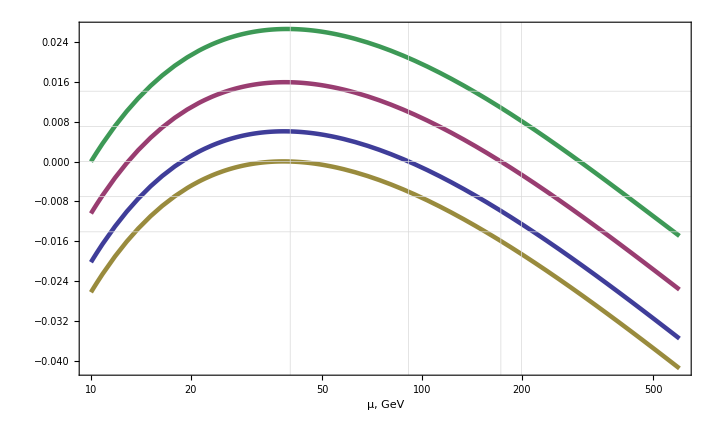

```mathematica
LogLinearPlot[{ScaleDep[PDG`MZ][MT,x]/PDG`MT-1,ScaleDep[PDG`MT][MT,x]/PDG`MT-1,ScaleDep[40][MT,x]/PDG`MT-1,ScaleDep[300][MT,x]/PDG`MT-1},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{0,-PDG`dMT/PDG`MT,-2PDG`dMT/PDG`MT,+PDG`dMT/PDG`MT,+2PDG`dMT/PDG`MT}},ImageSize->{72 10,72 7}]
```

```mathematica
EstimateTheorUncertainty[Sequence @@ (Last /@ sol[PDG`MZ][])]
```

{0.3586626304561123155,0.6477079655285805314,1.161293213030017322,0.946987214269128843,0.1266158332265555917,132.4093967768038963,182.3752000000000066,2}

(91.18760000000000717 | 0.0000224608564930277 | 0.0009477878405394346
80.38499999999996721 | 0.0000296293090979903 | 0.0009942871228845826
173.20999999999996 | -0.01081840760123 | 0.0057604775843616
125.7000000000000184 | 0.00116111628925567 | -0.000719608686289938
0.00001166378700000000619 | -0.004235520878445559 | -0.000629517918260365)

```mathematica
EstimateTheorUncertainty[Sequence @@ (Last /@ sol[PDG`MT][])]
```

{0.3609021115346426776,0.6456062317682658074,1.117952645156373051,0.9265856779548876017,0.1132472843757865877,133.9158922969686749,346.4200000000000159,2}

(91.18759999999986424 | 0.001323846895572077 | 0.000134571831976795
80.3849999999998958 | 0.001254615626271249 | 0.000128187744177326
173.2099999999997785 | -0.013686736834933301 | 0.01056009139671077
125.7000000000000205 | 0.001672126867998785 | -0.00117354266176821
0.00001166378700000001095 | -0.01011129689358631 | 0.003986855255409544)

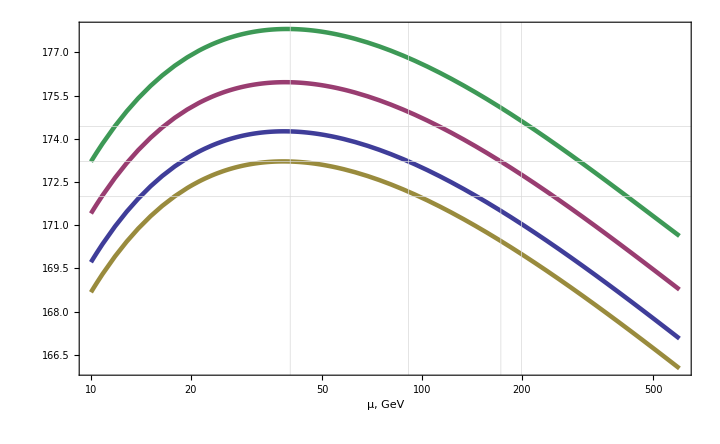

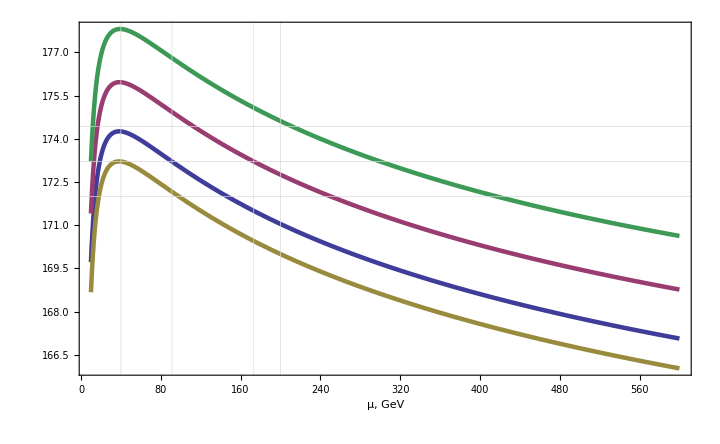

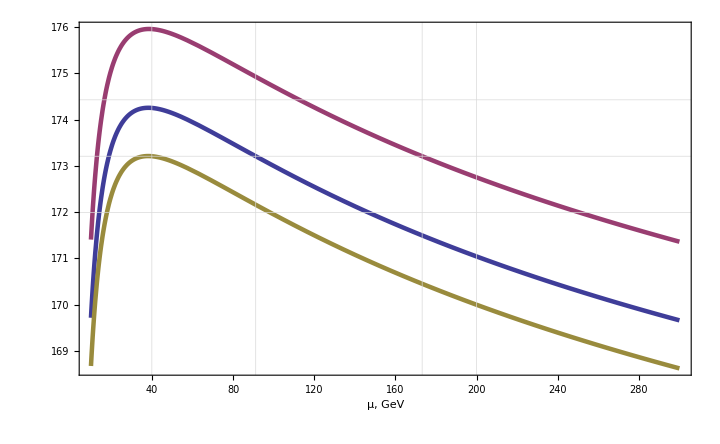

```mathematica
LogLinearPlot[{ScaleDep[PDG`MZ][MT,x],ScaleDep[PDG`MT][MT,x],ScaleDep[40][MT,x],ScaleDep[300][MT,x]},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{PDG`MT,PDG`MT-PDG`dMT,PDG`MT+PDG`dMT}},ImageSize->{72 10,72 7}]
```

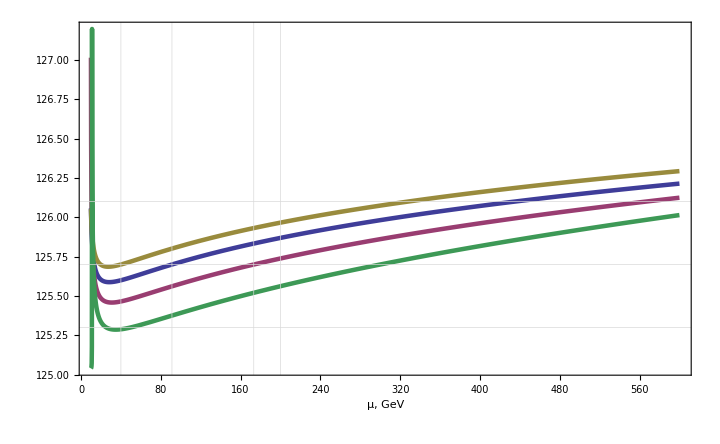

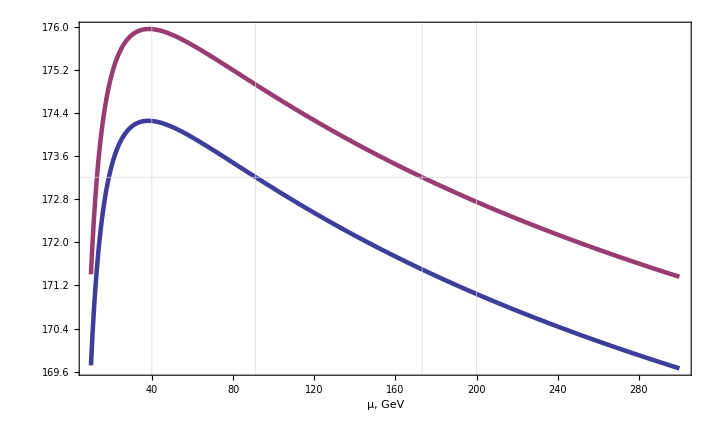

```mathematica
Plot[{ScaleDep[PDG`MZ][MH,x],ScaleDep[PDG`MT][MH,x],ScaleDep[40][MH,x],ScaleDep[300][MH,x]},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{PDG`MH,PDG`MH-PDG`dMH,PDG`MH+PDG`dMH}},ImageSize->{72 10,72 7}]
```

FindRoot::nlnum: The function value TraditionalForm`{-91.1876 + MZ(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -80.385 + MW(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -173.21 + MT(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -125.7 + MH(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -0.0000116638 + GF(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), 0.108301  - 1.\ RunQCD(x, 0.1185, 91.1876, 4., 173.21)}
 is not a list of numbers with dimensions TraditionalForm`{6} at TraditionalForm`{gp, g, gs, yt, lam, mu0} = TraditionalForm`{0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03}.

Join::heads: Heads TraditionalForm`FindRoot and TraditionalForm`List at positions TraditionalForm`1 and TraditionalForm`2 are expected to be the same.

FindRoot::nlnum: The function value TraditionalForm`{-91.1876 + MZ(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -80.385 + MW(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -173.21 + MT(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -125.7 + MH(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -0.0000116638 + GF(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), 0.108301  - 1.\ RunQCD(x, 0.1185, 91.1876, 4., 173.21)}
 is not a list of numbers with dimensions TraditionalForm`{6} at TraditionalForm`{gp, g, gs, yt, lam, mu0} = TraditionalForm`{0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03}.

Join::heads: Heads TraditionalForm`FindRoot and TraditionalForm`List at positions TraditionalForm`1 and TraditionalForm`2 are expected to be the same.

FindRoot::nlnum: The function value TraditionalForm`{-91.1876 + MZ(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -80.385 + MW(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -173.21 + MT(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -125.7 + MH(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -0.0000116638 + GF(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), 0.108301  - 1.\ RunQCD(x, 0.1185, 91.1876, 4., 173.21)}
 is not a list of numbers with dimensions TraditionalForm`{6} at TraditionalForm`{gp, g, gs, yt, lam, mu0} = TraditionalForm`{0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

Join::heads: Heads TraditionalForm`FindRoot and TraditionalForm`List at positions TraditionalForm`1 and TraditionalForm`2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

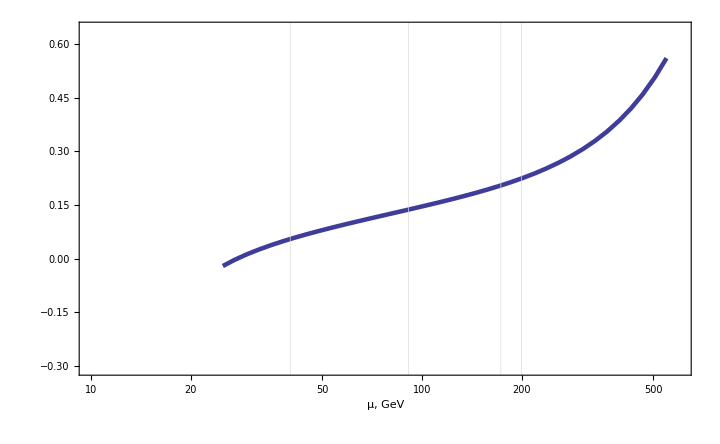

```mathematica
LogLinearPlot[{LogMuDerivative[MH,x],LogMuDerivative[MH,x],LogMuDerivative[MH,x],LogMuDerivative[MH,x]},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{-PDG`dMH,PDG`MH/PDG`MH}},ImageSize->{72 10,72 7}]
```